```mathematica
Vehicle[δ1_,β_,{tstart_,tend_},initialValues_]:=Block[{βr,η,δ ,δ2,rules,q,q1,q2,q3,Eq1,Eq2,Eq3,motionEq,solution,vars,initVars},
Brake1[t_,τ1_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ1)]);
Brake[t_,τ01_,τ1_,βr_]:=
Fold[Plus,0,Table[Brake1[t-τ01⟦k⟧,τ1⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
βr= β;
(*q= Import["1.dat"];
q1 = DeleteCases[Table[If[q[[k,1]] == q[[k+1,1]], null ,q[[k+1]]],{k,1,Length[q]-1}],null];
q2 = Map[({First[#]+0.463584,Last[#]})&,q1];
q3 = Interpolation[q2];
δ2 = q3[t];*)

δ =δ1;(*If[drivingModel == True, δ1,δ1+δ2];*)
η = √(1.0-βr^2);
vars={x[t],x'[t],y[t],y'[t],ψ[t],ψ'[t]};
initVars=vars/.t->tstart;
initCond=Thread[initVars==initialValues];

rules =
{C1->80000.0,C2->80000.0,C3->80000.0,C4->80000.0,
μ1->0.5,μ2->0.5,μ3->0.5,μ4->0.5,
Fz1->26719.0,Fz2->26719.0,Fz3->21295.0,Fz4->21295.0(*NOT SURE*),
m ->2050.0,ωt->1.63,lf->1.43,lr->1.47 , Jz -> 3344.0 };

f1[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
αsl1=f1[μ1,Fz1,C1]; αsl2=f1[μ2,Fz2,C2];
αsl3=f1[μ3,Fz3,C3]; αsl4=f1[μ4,Fz4,C4];

f2[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
α1=f2[δ,lf]; α2=f2[δ,lf];
α3=f2[0,-lr]; α4=f2[0,-lr];

f3[C_,α_,μ_,F_,αs_]:=Piecewise[{{- C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3, Abs[α]<αs}, {-η μ F Sign[α], Abs[α]≥αs}}];
fy1=f3[C1,α1,μ1,Fz1,αsl1]/.rules; fy2=f3[C2,α2,μ2,Fz2,αsl2]/.rules;
fy3=f3[C3,α3,μ3,Fz3,αsl3]/.rules; fy4=f3[C4,α4,μ4,Fz4,αsl4]/.rules;

f4[μ_,F_]:=βr μ F/.rules;
fx1=f4[μ1,Fz1]/.rules; fx2=f4[μ2,Fz2]/.rules;
fx3=f4[μ3,Fz3]/.rules; fx4=f4[μ4,Fz4]/.rules;

Fx1 =fx1 Cos[δ] - fy1 Sin[δ]; Fx2 =fx2 Cos[δ] - fy2 Sin[δ];
Fx3 =fx3 Cos[0] - fy3 Sin[0]; Fx4 =fx4 Cos[0] - fy4 Sin[0];

Fy1 =fx1 Sin[δ] + fy1 Cos[δ]; Fy2 =fx2 Sin[δ] + fy2 Cos[δ];
Fy3 =fx3 Sin[0] + fy3 Cos[0]; Fy4 =fx4 Sin[0] + fy4 Cos[0];

Eq1 = m x''[t]== m y'[t]ψ'[t] + Fx1 +Fx2 +Fx3 +Fx4;
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Fy1+ Fy2+ Fy3+ Fy4;
Eq3 =Jz ψ''[t] == lf(Fy1 + Fy2) - lr(Fy3 + Fy4) + (ωt/2)( Fx2 -Fx1 - Fx3 + Fx4);
motionEq ={Eq1,Eq2,Eq3}/.rules;
(*Print["motionEq = ",motionEq];*)
solution = NDSolve[Flatten[{motionEq/.rules,initCond}],{x,y,ψ},{t,tstart,tend}];
{solution,x[t]/.solution,y[t]/.solution,ψ[t]/.solution,(vars/.Flatten[solution]/.t->tend)}
]
```

```mathematica
costFunction1[δ1_?NumericQ,,β_?NumericQ,{tstart_,tend_},initialValues_,idealRoad_]:=Block[{solution,V1,psi,pl1,vars,xk,yk},
V1 = Vehicle[δ1,β,{tstart,tend},initialValues];
    solution=V1[[1]];
vars = Last[V1];
xk = V1[[2]];
yk = V1[[3]];
psi = V1[[4]];
Print[vars];
{solution,vars,xk,yk,psi}
]
```

```mathematica
costFunction2[δ1_?NumericQ,β_?NumericQ,{tstart_,tend_},initialValues_,idealRoad_,vmax_,wigths_List]:=Block[{solution,pl1,V1,ΔxVec,lineElement,initVars,vars,velocity,tangent,cosθ,xx,yy,slpAngleLimit=4./(2π),dψ},
(* --- the ideal line of the car is given as a polynomial --- *)
pl1=idealRoad;
V1 = Vehicle[δ1,β,{tstart,tend},initialValues];
(* equations of motion *)
  

 solution=V1[[1]];
(* determine the vector for the line element *)
xx = First[V1[[2]]/.Flatten[solution]/.t->tend];
yy = First[V1[[3]]/.Flatten[solution]/.t->tend];
(*Print["x is --",xx];
Print["y is --",yy];*)
ΔxVec={xx-(x1/.Flatten[FindRoot[yy==pl1,{x1,xx}]]),((pl1/.x1->xx)- yy/.Flatten[solution]/.t->tend)};
lineElement=ΔxVec;
(*Print["lineElement = ",lineElement];*)
(* calculate the line element at the endpoint of the interval *)
(*lineElement=ΔxVec/.Flatten[solution]/.t->tend;*)
(* determine the velocity vector *)
(* here you need the symbolic dependencies !!!!!!!!!! *)
velocity=Flatten[{D[x[t],t],D[y[t],t]}/.Flatten[solution]/.t->tend];
(* calculate the tangent vector to the ideal line o the road *)
tangent={1,D[pl1, x1]}/.x1->xx;
(* the cos of the angle between velocity and tangent line of the road *)
cosθ=(tangent.velocity)/(Norm[tangent] Norm[velocity]);
(* slip angle evaluation  *)
α11=α1+δ1/.Flatten[solution]/.t->tend;
α21=α2+δ1/.Flatten[solution]/.t->tend;
α31=α3/.Flatten[solution]/.t->tend;
α41=α4/.Flatten[solution]/.t->tend;
dψ=(D[ψ[t],t])^2/.Flatten[solution]/.t->tend;
(* here follows the cost function *)
Part[wigths,1](√(lineElement.Conjugate[lineElement]))^2+Part[wigths,2]((1-cosθ)^2+dψ)+Part[wigths,3]((vmax/.x1->xx )- (velocity.velocity)^0.5)^2+Part[wigths,4]((4-(Tanh[100(β-1)]-Tanh[100(β+1)])^2)
+(4-(Tanh[100(α11-slpAngleLimit)]-Tanh[100(α11+slpAngleLimit)])^2)+(4-(Tanh[100(α21-slpAngleLimit)]-Tanh[100(α21+slpAngleLimit)])^2))+(4-(Tanh[100(α31-slpAngleLimit)]-Tanh[100(α31+slpAngleLimit)])^2)+(4-(Tanh[100(α41-slpAngleLimit)]-Tanh[100(α41+slpAngleLimit)])^2)]
```

```mathematica
Options[optimalPath] = {exportResultsTo ->{"ResultsCar_001.m"}};
```

```mathematica
optimalPath[initialVals_,idealRoad_,{tstart_,tend_},numberOfDivisions_,wigths_List,vmax_,OptionsPattern[]]:=Block[{δt,β1,initVal,minval,δ1,αx1,αx2,αx3,αx4,ts,te,cf1,counter,solutions={},δt1,δt1max,carLocation,roadLocation,dist,fileName,vΔ,exportData},
(* --- fix time step --- *)
(*vmax   = idealRoad[[2]];*)
fileName=OptionValue[exportResultsTo];
δt1=(tend-tstart)/numberOfDivisions;
δt1max=δt1;
initVal=initialVals;
ts=tstart;
te=ts+δt1;
counter=0;
(* -- loop over the time interval -- *)
While[te<tend,
Print["--- Minimum search --- ", counter," te = ",te];
(* -- find optimal parameters -- *)
minval=AbsoluteTiming[FindMinimum[{costFunction2[δ,β,{ts,te},initVal,idealRoad[[1]],vmax,wigths],-0.5≤δ≤0.5&&-1.≤ β≤1.&&0.01 δt1max≤δt≤4δt1max},{δ,β,δt}]];
Print["search time = ",First[minval]," sec"];
minval=Last[minval];
Print["minval = {min,δ,β,δt} = ",minval];
(* --- use optimal parametsrs for the solution --- *)
δ1=δ/.Last[minval];
β1 = β/.Last[minval];
δt1=δt/.Last[minval];

cf1=Vehicle[δ1,β1,{ts,te},initVal];
αx1=α1/.Flatten[cf1⟦1⟧]/.t->te;
αx2=α2/.Flatten[cf1⟦1⟧]/.t->te;
αx3=α3/.Flatten[cf1⟦1⟧]/.t->te;
αx4=α4/.Flatten[cf1⟦1⟧]/.t->te;
carLocation={x[t],y[t]}/.cf1⟦1⟧/.t->te;
roadLocation={x[t],(idealRoad[[1]]/.x1->x[t])}/.cf1⟦1⟧/.t->te;
dist=√Norm[carLocation-roadLocation];
vΔ=Abs[vmax-√(initVal⟦2⟧^2+initVal⟦4⟧^2)];
(*Print[cf1[[4]]/.Flatten[cf1[[1]]]/.t->te];*)
(* --- collect the solutions --- *)
AppendTo[solutions,{{ts,te},cf1⟦1⟧,δ1,β1,dist,vΔ,First[minval],αx1,αx2,αx3,αx4,(ψ[t]/.Flatten[cf1[[1]]]/.t->te)}];
Print[plotResults[solutions,First[idealRoad],idealLineRoad1]];
(* --- update the initial conditions --- *)
initVal=Last[cf1];
Print["v = ",√(initVal⟦2⟧^2+initVal⟦4⟧^2)];
Print[initVal];
ts=te;
te=te+δt1;
counter=counter+1;
];
exportData={{initialVals,idealRoad,{tstart,tend},numberOfDivisions,wigths,vmax},solutions};
Print["file = ",fileName];
If[Length[fileName]>0,Export[fileName,exportData]];
solutions
]
```

```mathematica
obstacelCurve[x0_,xend_,eps_,x_,f_]:=Block[{data,g,α,slope,Δ,xm,vmax},
(* define the somehow the midpoint of an interval *)
xm=(1(xend-x0))/2+x0;
f10=Apply[Function,{x,f}];
(* determine the slope of the curve at this midpoint *)
slope=-1/N[D[f10[x],x]/.x->xm];
α=Abs[ArcTan[slope]];
If[slope>0,Δ=xm+eps Cos[α],Δ=xm-eps Cos[α]];
(* set up three points for interpolation using not only the function value but also the first derivative *)data={{{x0},f10[x0],(D[f10[x],x]/.x->x0)},{{Δ},f10[xm]+Abs[Sin[α]]eps,-1/slope},{{xend},f10[xend],(D[f10[x],x]/.x->xend)}};
(* generate the interpolation function *)
g=Interpolation[data];
(* define a picewise function for the obstacle curve *)
{Piecewise[{{g[x],x0≤x≤xend},{f10[x],x>xend||x<x0}}],Piecewise[{{vmax = 2, x0≤x ≤ xend},{vmax = 8, x>xend||x<x0}}]}
]
```

```mathematica
plotResults[sols_,idealLineRoad2_,idealLineRoad1_]:=Block[{plots,pl0,pl1,pl2,pl3,pl4,pl5,pl6,pl7,pl8,pl9,pl10,pl11,pl12,pl13,xend},
plots=Map[Apply[ParametricPlot,{{x[t],y[t]}/.Flatten[#⟦2⟧],Prepend[First[#],t]}]&,sols];
xend=First[(x[t]/.Part[Last[sols],2]/.t->Last[First[Last[sols]]])];
pl0=Plot[{idealLineRoad2,idealLineRoad1+4,idealLineRoad1-4},{x1,0,xend},PlotStyle->{Red,Blue,Blue},PlotPoints->100];
pl1=Show[{pl0,plots},PlotRange->All];
pl2=ListPlot[Map[{#⟦1,2⟧-#⟦1,1⟧,#⟦3⟧}&,sols],Frame->True,FrameLabel->{"Δt","δ"},Joined->False,PlotRange->All, InterpolationOrder->2];
pl3=ListPlot[Map[{#⟦1,2⟧,#⟦3⟧}&,sols],Frame->True,FrameLabel->{"t","δ"},Joined->True,PlotRange->All];
pl4=ListPlot[Map[{#⟦1,2⟧-#⟦1,1⟧,#⟦4⟧}&,sols],Frame->True,FrameLabel->{"Δt","β"},Joined->False,PlotRange->All, InterpolationOrder->2];
pl5=ListPlot[Map[{#⟦1,2⟧,#⟦4⟧}&,sols],Frame->True,FrameLabel->{"t","β"},Joined->True,PlotRange->All];
pl6=ListPlot[Map[{#⟦1,2⟧,#⟦5⟧}&,sols],Frame->True,FrameLabel->{"t","Δ"},Joined->True,PlotRange->All];
pl7=ListPlot[Map[{#⟦1,2⟧,#⟦6⟧}&,sols],Frame->True,FrameLabel->{"t","Δv"},Joined->True,PlotRange->All];
pl8=ListPlot[Map[{#⟦1,2⟧,#⟦7⟧}&,sols],Frame->True,FrameLabel->{"t","cost"},Joined->True,PlotRange->All];
pl9=ListPlot[Map[{#⟦1,2⟧,#⟦8⟧}&,sols],Frame->True,FrameLabel->{"t","α1"},Joined->True,PlotRange->All];
pl10=ListPlot[Map[{#⟦1,2⟧,#⟦9⟧}&,sols],Frame->True,FrameLabel->{"t","α2"},Joined->True,PlotRange->All];
pl11=ListPlot[Map[{#⟦1,2⟧,#⟦10⟧}&,sols],Frame->True,FrameLabel->{"t","α3"},Joined->True,PlotRange->All];
pl12=ListPlot[Map[{#⟦1,2⟧,#⟦11⟧}&,sols],Frame->True,FrameLabel->{"t","α4"},Joined->True,PlotRange->All];
pl13=ListPlot[Map[{#⟦1,2⟧,#⟦12⟧}&,sols],Frame->True,FrameLabel->{"t","ψ"},Joined->True,PlotRange->All];
GraphicsGrid[{{pl1,pl8},{pl2,pl4},{pl3,pl5},{pl6,pl7},{pl8,pl9},{pl10,pl11},{pl12,pl13}}]
]
```

```mathematica
carModel1[x_,y_,θ_]:=Block[{},Graphics[{Translate[Rotate[Translate[{{Opacity[.4],Hue[1],Polygon[{{0,0},{2.5,0},{2.5,1.2},{0,1.2},{0,0}}]},{Rectangle[{0,0},{.75,.25}]},{Rectangle[{1.75,0},{2.5,.25}]},{Rectangle[{0,1.2},{.75,.95}]},{Rectangle[{1.75,1.2},{2.5,.95}]},{{Yellow,Disk[{1.25,.6},{1.2,.5}]}},{{Orange,Disk[{1.65,.6},{.2,.45}]}},{Disk[{1.25,0.6},.2,{Pi/4,3Pi/4}]},{Disk[{1.25,0.6},.2,{Pi/4+π,3Pi/4+π}]},{Circle[{1.25,.6},.2]}},{x,y}],θ],{-1.25,-.6}]},AspectRatio->Automatic]]
```

```mathematica
plotCarMotion[sols_,idealLineRoad2_]:=Block[{xend,idealLineRoad1,laneWidth=2},
xend=First[(x[t]/.Part[Last[sols],2]/.t->Last[First[Last[sols]]])];
idealLineRoad1=First[Last[First[First[idealLineRoad2]]]];
pl0=Plot[Evaluate[{First[idealLineRoad2],idealLineRoad1+laneWidth,idealLineRoad1-laneWidth,idealLineRoad1+3laneWidth,}],{x1,0,3xend},PlotStyle->{Red,Blue,Blue,Blue},PlotPoints->100];
track=Apply[Function,{t,Piecewise[Map[{{x[t],y[t],ψ[t]}/.Flatten[#⟦2⟧],First[First[#]]≤t<Last[First[#]]}&,sols]]}];
Manipulate[Show[{pl0,Apply[carModel1,track[t]]},AspectRatio->Automatic,PlotRange->All],{t,0,Last[First[Last[sols]]]}]
]
```

```mathematica
importResults[fileName_]:=Block[{initialVals,idealRoad,tstart,tend,numberOfDivisions,wigths,vmax,solutions,data,lengthData},
(* --- import data structure --- *)
Print[" --- reading data ..."];
data=Import[fileName];
lengthData=Length[Flatten[data]];
Print[" --- processing data ..."];
If[lengthData>1,
{{initialVals,idealRoad,{tstart,tend},numberOfDivisions,wigths,vmax},solutions}=data,
(* If branch *)
{{initialVals,idealRoad,{tstart,tend},numberOfDivisions,wigths,vmax},solutions}=data;

];

{{initialVals,idealRoad,{tstart,tend},numberOfDivisions,wigths,vmax},solutions}
]
```

```mathematica
plotImportData[sol0_]:=Block[{},
plotResults[Last[sol0],First[sol0]⟦2,1⟧,First[Last[First[First[sol0]⟦2,1⟧]]]]]
```

```mathematica
points={{0,0},{700,-40}};
idealLineRoad1=-1/20 x1;
idealLineRoad2=obstacelCurve[2,5,0,x1,-x1/20]
```

{Piecewise[{{InterpolatingFunction[{{2., 5.}}, <>][x1], 2≤x1≤5}, {-x1/20, x1>5||x1<2}, {0, True}}],Piecewise[{{2, 2≤x1≤5}, {8, x1>5||x1<2}, {0, True}}]}

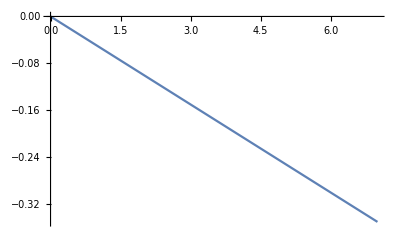

```mathematica
Plot[idealLineRoad2⟦1⟧,{x1,0,7}]
```

```mathematica
SetDirectory["F:\\Master\\Mathematica Files\\M-Files"]
```

F:\Master\Mathematica Files\M-Files

```mathematica
sols3 = optimalPath[{0.01,13,0.1,0.50,0.00,0},idealLineRoad2,{0,1.},150,{0.45,0.45,.1,1},12.5,exportResultsTo ->{"ResultsCar_SlipAngle_002f.m"}]
```

```mathematica
FileNames["*.m"]
```

{29.m}

## Low Speed Straigth Lane 3 m/s

--- reading data ...

--- processing data ...

Part::partw: Part 8 of {{0, 0.018}, « 5 », 2.17864} does not exist.

Part::partw: Part 8 of {{0.018, 0.05366}, « 5 », 1.60449} does not exist.

Part::partw: Part 8 of {{0.05366, 0.0825715}, {{« 1 »}}, 2.96282, -0.175156, 0.240485, 0.299796, 0.606754} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

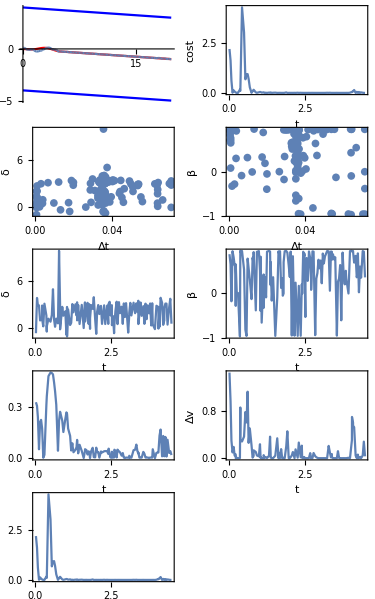

```mathematica
sol0=importResults["29.m"];
plotImportData[sol0]
```

```mathematica
Length[sol0⟦1⟧]
```

6

```mathematica
Table[sol0⟦1,k⟧,{k,1,Length[sol0⟦1⟧]}]
```

{{0.01,3,0.1,0.5,0.,0},{Piecewise[{{InterpolatingFunction[{{1., 5.}}, <>][x1], 1≤x1≤5}, {-x1/20, x1>5||x1<1}, {0, True}}],Piecewise[{{2, 1≤x1≤5}, {8, x1>5||x1<1}, {0, True}}]},{0,4.5},250,{0.45,0.45,0.1,1},4.5}

```mathematica
dat = Table[sol0⟦2,k⟧,{k,1,Length[sol0⟦2⟧]}]
```

{{{0,0.018},{{x→InterpolatingFunction[{{0., 0.018}}, <>],y→InterpolatingFunction[{{0., 0.018}}, <>],ψ→InterpolatingFunction[{{0., 0.018}}, <>]}},-0.618024,0.8793,0.327883,1.45862,2.17864},{{0.018,0.05366},{{x→InterpolatingFunction[{{0.018, 0.05366}}, <>],y→InterpolatingFunction[{{0.018, 0.05366}}, <>],ψ→InterpolatingFunction[{{0.018, 0.05366}}, <>]}},3.88584,0.656477,0.306634,0.964496,1.60449},{{0.05366,0.0825715},{{x→InterpolatingFunction[{{0.05366, 0.0825715}}, <>],y→InterpolatingFunction[{{0.05366, 0.0825715}}, <>],ψ→InterpolatingFunction[{{0.05366, 0.0825715}}, <>]}},2.96282,-0.175156,0.240485,0.299796,0.606754},{{0.0825715,0.119062},{{x→InterpolatingFunction[{{0.0825715, 0.119062}}, <>],y→InterpolatingFunction[{{0.0825715, 0.119062}}, <>],ψ→InterpolatingFunction[{{0.0825715, 0.119062}}, <>]}},2.93845,0.945849,0.052212,0.0978078,0.00806212},{{0.119062,0.155209},{{x→InterpolatingFunction[{{0.119062, 0.155209}}, <>],y→InterpolatingFunction[{{0.119062, 0.155209}}, <>],ψ→InterpolatingFunction[{{0.119062, 0.155209}}, <>]}},1.01703,0.810634,0.211029,0.192386,0.127503},{{0.155209,0.188043},{{x→InterpolatingFunction[{{0.155209, 0.188043}}, <>],y→InterpolatingFunction[{{0.155209, 0.188043}}, <>],ψ→InterpolatingFunction[{{0.155209, 0.188043}}, <>]}},1.07502,0.625866,0.224693,0.0459774,0.0671034},{{0.188043,0.220866},{{x→InterpolatingFunction[{{0.188043, 0.220866}}, <>],y→InterpolatingFunction[{{0.188043, 0.220866}}, <>],ψ→InterpolatingFunction[{{0.188043, 0.220866}}, <>]}},1.40003,0.648911,0.176096,0.0663668,0.025192},{{0.220866,0.223813},{{x→InterpolatingFunction[{{0.220866, 0.223813}}, <>],y→InterpolatingFunction[{{0.220866, 0.223813}}, <>],ψ→InterpolatingFunction[{{0.220866, 0.223813}}, <>]}},2.92049,-0.278412,0.168466,0.0224559,0.0223305},{{0.223813,0.224767},{{x→InterpolatingFunction[{{0.223813, 0.224767}}, <>],y→InterpolatingFunction[{{0.223813, 0.224767}}, <>],ψ→InterpolatingFunction[{{0.223813, 0.224767}}, <>]}},1.13764,0.645897,0.165999,0.0000351373,0.0214945},{{0.224767,0.259856},{{x→InterpolatingFunction[{{0.224767, 0.259856}}, <>],y→InterpolatingFunction[{{0.224767, 0.259856}}, <>],ψ→InterpolatingFunction[{{0.224767, 0.259856}}, <>]}},0.259163,-0.0135608,0.00249017,0.00586775,0.0000500097},{{0.259856,0.298354},{{x→InterpolatingFunction[{{0.259856, 0.298354}}, <>],y→InterpolatingFunction[{{0.259856, 0.298354}}, <>],ψ→InterpolatingFunction[{{0.259856, 0.298354}}, <>]}},3.1525,0.0109058,0.0195756,0.000236268,0.0000955293},{{0.298354,0.362488},{{x→InterpolatingFunction[{{0.298354, 0.362488}}, <>],y→InterpolatingFunction[{{0.298354, 0.362488}}, <>],ψ→InterpolatingFunction[{{0.298354, 0.362488}}, <>]}},1.64581,-0.962948,0.312119,0.00101219,0.164794},{{0.362488,0.375687},{{x→InterpolatingFunction[{{0.362488, 0.375687}}, <>],y→InterpolatingFunction[{{0.362488, 0.375687}}, <>],ψ→InterpolatingFunction[{{0.362488, 0.375687}}, <>]}},-0.411219,0.954925,0.35984,0.86369,0.104096},{{0.375687,0.376385},{{x→InterpolatingFunction[{{0.375687, 0.376385}}, <>],y→InterpolatingFunction[{{0.375687, 0.376385}}, <>],ψ→InterpolatingFunction[{{0.375687, 0.376385}}, <>]}},0.26225,0.932712,0.362239,0.304398,0.102465},{{0.376385,0.431763},{{x→InterpolatingFunction[{{0.376385, 0.431763}}, <>],y→InterpolatingFunction[{{0.376385, 0.431763}}, <>],ψ→InterpolatingFunction[{{0.376385, 0.431763}}, <>]}},1.23567,0.950427,0.480899,0.284033,4.24891},{{0.431763,0.498551},{{x→InterpolatingFunction[{{0.431763, 0.498551}}, <>],y→InterpolatingFunction[{{0.431763, 0.498551}}, <>],ψ→InterpolatingFunction[{{0.431763, 0.498551}}, <>]}},0.852584,0.538527,0.50176,0.368209,3.00751},{{0.498551,0.542628},{{x→InterpolatingFunction[{{0.498551, 0.542628}}, <>],y→InterpolatingFunction[{{0.498551, 0.542628}}, <>],ψ→InterpolatingFunction[{{0.498551, 0.542628}}, <>]}},1.70489,-0.812401,0.499041,0.786672,0.674562},{{0.542628,0.580268},{{x→InterpolatingFunction[{{0.542628, 0.580268}}, <>],y→InterpolatingFunction[{{0.542628, 0.580268}}, <>],ψ→InterpolatingFunction[{{0.542628, 0.580268}}, <>]}},4.99751,-0.951513,0.491264,0.60899,0.912261},{{0.580268,0.616224},{{x→InterpolatingFunction[{{0.580268, 0.616224}}, <>],y→InterpolatingFunction[{{0.580268, 0.616224}}, <>],ψ→InterpolatingFunction[{{0.580268, 0.616224}}, <>]}},1.13562,0.780391,0.444729,1.13306,0.935416},{{0.616224,0.649168},{{x→InterpolatingFunction[{{0.616224, 0.649168}}, <>],y→InterpolatingFunction[{{0.616224, 0.649168}}, <>],ψ→InterpolatingFunction[{{0.616224, 0.649168}}, <>]}},0.206098,0.566092,0.393133,0.26073,0.699327},{{0.649168,0.688939},{{x→InterpolatingFunction[{{0.649168, 0.688939}}, <>],y→InterpolatingFunction[{{0.649168, 0.688939}}, <>],ψ→InterpolatingFunction[{{0.649168, 0.688939}}, <>]}},1.25042,0.309364,0.313177,0.506826,0.277179},{{0.688939,0.745111},{{x→InterpolatingFunction[{{0.688939, 0.745111}}, <>],y→InterpolatingFunction[{{0.688939, 0.745111}}, <>],ψ→InterpolatingFunction[{{0.688939, 0.745111}}, <>]}},0.640897,-0.127343,0.0435808,0.221015,0.00276231},{{0.745111,0.780861},{{x→InterpolatingFunction[{{0.745111, 0.780861}}, <>],y→InterpolatingFunction[{{0.745111, 0.780861}}, <>],ψ→InterpolatingFunction[{{0.745111, 0.780861}}, <>]}},9.90484,0.800958,0.218169,0.00881424,0.0841786},{{0.780861,0.8144},{{x→InterpolatingFunction[{{0.780861, 0.8144}}, <>],y→InterpolatingFunction[{{0.780861, 0.8144}}, <>],ψ→InterpolatingFunction[{{0.780861, 0.8144}}, <>]}},3.06758,0.661608,0.271433,0.0387833,0.15439},{{0.8144,0.815041},{{x→InterpolatingFunction[{{0.8144, 0.815041}}, <>],y→InterpolatingFunction[{{0.8144, 0.815041}}, <>],ψ→InterpolatingFunction[{{0.8144, 0.815041}}, <>]}},-0.120883,0.926273,0.272042,0.133865,0.155207},{{0.815041,0.886371},{{x→InterpolatingFunction[{{0.815041, 0.886371}}, <>],y→InterpolatingFunction[{{0.815041, 0.886371}}, <>],ψ→InterpolatingFunction[{{0.815041, 0.886371}}, <>]}},2.7498,-0.379234,0.220195,0.105967,0.0257541},{{0.886371,0.923117},{{x→InterpolatingFunction[{{0.886371, 0.923117}}, <>],y→InterpolatingFunction[{{0.886371, 0.923117}}, <>],ψ→InterpolatingFunction[{{0.886371, 0.923117}}, <>]}},1.61593,0.932772,0.153319,0.0458048,0.00491181},{{0.923117,0.987316},{{x→InterpolatingFunction[{{0.923117, 0.987316}}, <>],y→InterpolatingFunction[{{0.923117, 0.987316}}, <>],ψ→InterpolatingFunction[{{0.923117, 0.987316}}, <>]}},2.17735,0.948547,0.22937,0.0313524,0.0295138},{{0.987316,1.02412},{{x→InterpolatingFunction[{{0.987316, 1.02412}}, <>],y→InterpolatingFunction[{{0.987316, 1.02412}}, <>],ψ→InterpolatingFunction[{{0.987316, 1.02412}}, <>]}},-0.823865,0.509358,0.268534,0.237358,0.0458083},{{1.02412,1.044},{{x→InterpolatingFunction[{{1.02412, 1.044}}, <>],y→InterpolatingFunction[{{1.02412, 1.044}}, <>],ψ→InterpolatingFunction[{{1.02412, 1.044}}, <>]}},2.73561,-0.392304,0.260302,0.00604503,0.043012},{{1.044,1.04459},{{x→InterpolatingFunction[{{1.044, 1.04459}}, <>],y→InterpolatingFunction[{{1.044, 1.04459}}, <>],ψ→InterpolatingFunction[{{1.044, 1.04459}}, <>]}},-1.02693,0.823254,0.259707,0.0150846,0.0427047},{{1.04459,1.07971},{{x→InterpolatingFunction[{{1.04459, 1.07971}}, <>],y→InterpolatingFunction[{{1.04459, 1.07971}}, <>],ψ→InterpolatingFunction[{{1.04459, 1.07971}}, <>]}},2.40889,-0.654076,0.173861,0.000371435,0.0129618},{{1.07971,1.1438},{{x→InterpolatingFunction[{{1.07971, 1.1438}}, <>],y→InterpolatingFunction[{{1.07971, 1.1438}}, <>],ψ→InterpolatingFunction[{{1.07971, 1.1438}}, <>]}},0.443748,0.424848,0.131988,0.00231216,0.0276169},{{1.1438,1.14543},{{x→InterpolatingFunction[{{1.1438, 1.14543}}, <>],y→InterpolatingFunction[{{1.1438, 1.14543}}, <>],ψ→InterpolatingFunction[{{1.1438, 1.14543}}, <>]}},0.431197,-0.323148,0.131553,0.0517727,0.0287463},{{1.14543,1.1811},{{x→InterpolatingFunction[{{1.14543, 1.1811}}, <>],y→InterpolatingFunction[{{1.14543, 1.1811}}, <>],ψ→InterpolatingFunction[{{1.14543, 1.1811}}, <>]}},0.704726,0.369956,0.0451286,0.00906178,0.000858089},{{1.1811,1.21883},{{x→InterpolatingFunction[{{1.1811, 1.21883}}, <>],y→InterpolatingFunction[{{1.1811, 1.21883}}, <>],ψ→InterpolatingFunction[{{1.1811, 1.21883}}, <>]}},3.1095,-0.0321233,0.0872622,0.0156279,0.0104811},{{1.21883,1.22546},{{x→InterpolatingFunction[{{1.21883, 1.22546}}, <>],y→InterpolatingFunction[{{1.21883, 1.22546}}, <>],ψ→InterpolatingFunction[{{1.21883, 1.22546}}, <>]}},3.05622,-0.0876124,0.0738187,0.0130573,0.00536658},{{1.22546,1.25667},{{x→InterpolatingFunction[{{1.22546, 1.25667}}, <>],y→InterpolatingFunction[{{1.22546, 1.25667}}, <>],ψ→InterpolatingFunction[{{1.22546, 1.25667}}, <>]}},2.05238,0.936566,0.0346964,0.00169927,0.000452865},{{1.25667,1.32108},{{x→InterpolatingFunction[{{1.25667, 1.32108}}, <>],y→InterpolatingFunction[{{1.25667, 1.32108}}, <>],ψ→InterpolatingFunction[{{1.25667, 1.32108}}, <>]}},3.07417,0.951576,0.0490693,0.0408039,0.0149854},{{1.32108,1.35684},{{x→InterpolatingFunction[{{1.32108, 1.35684}}, <>],y→InterpolatingFunction[{{1.32108, 1.35684}}, <>],ψ→InterpolatingFunction[{{1.32108, 1.35684}}, <>]}},1.65501,0.939541,0.0642567,0.366603,0.0036049},{{1.35684,1.37576},{{x→InterpolatingFunction[{{1.35684, 1.37576}}, <>],y→InterpolatingFunction[{{1.35684, 1.37576}}, <>],ψ→InterpolatingFunction[{{1.35684, 1.37576}}, <>]}},3.33037,0.187886,0.106546,0.0662683,0.0232634},{{1.37576,1.37666},{{x→InterpolatingFunction[{{1.37576, 1.37666}}, <>],y→InterpolatingFunction[{{1.37576, 1.37666}}, <>],ψ→InterpolatingFunction[{{1.37576, 1.37666}}, <>]}},1.02544,0.704712,0.107175,0.00936623,0.0238088},{{1.37666,1.41178},{{x→InterpolatingFunction[{{1.37666, 1.41178}}, <>],y→InterpolatingFunction[{{1.37666, 1.41178}}, <>],ψ→InterpolatingFunction[{{1.37666, 1.41178}}, <>]}},2.98029,-0.159893,0.0285056,0.00215942,0.000213865},{{1.41178,1.45798},{{x→InterpolatingFunction[{{1.41178, 1.45798}}, <>],y→InterpolatingFunction[{{1.41178, 1.45798}}, <>],ψ→InterpolatingFunction[{{1.41178, 1.45798}}, <>]}},0.558329,0.363275,0.0785997,0.000938247,0.00707867},{{1.45798,1.5294},{{x→InterpolatingFunction[{{1.45798, 1.5294}}, <>],y→InterpolatingFunction[{{1.45798, 1.5294}}, <>],ψ→InterpolatingFunction[{{1.45798, 1.5294}}, <>]}},3.00288,-0.951494,0.0425717,0.0424962,0.0125592},{{1.5294,1.5936},{{x→InterpolatingFunction[{{1.5294, 1.5936}}, <>],y→InterpolatingFunction[{{1.5294, 1.5936}}, <>],ψ→InterpolatingFunction[{{1.5294, 1.5936}}, <>]}},0.0398704,-0.0954872,0.000891083,0.33874,6.98669×10^-7},{{1.5936,1.63513},{{x→InterpolatingFunction[{{1.5936, 1.63513}}, <>],y→InterpolatingFunction[{{1.5936, 1.63513}}, <>],ψ→InterpolatingFunction[{{1.5936, 1.63513}}, <>]}},3.31829,0.94261,0.0420926,1.76899×10^-6,0.00151298},{{1.63513,1.639},{{x→InterpolatingFunction[{{1.63513, 1.639}}, <>],y→InterpolatingFunction[{{1.63513, 1.639}}, <>],ψ→InterpolatingFunction[{{1.63513, 1.639}}, <>]}},0.874221,0.913407,0.0526412,0.0927855,0.00138691},{{1.639,1.68563},{{x→InterpolatingFunction[{{1.639, 1.68563}}, <>],y→InterpolatingFunction[{{1.639, 1.68563}}, <>],ψ→InterpolatingFunction[{{1.639, 1.68563}}, <>]}},2.28726,0.945396,0.046901,0.00223961,0.00340269},{{1.68563,1.72172},{{x→InterpolatingFunction[{{1.68563, 1.72172}}, <>],y→InterpolatingFunction[{{1.68563, 1.72172}}, <>],ψ→InterpolatingFunction[{{1.68563, 1.72172}}, <>]}},3.26551,0.123776,0.0213299,0.154117,0.0000570571},{{1.72172,1.75697},{{x→InterpolatingFunction[{{1.72172, 1.75697}}, <>],y→InterpolatingFunction[{{1.72172, 1.75697}}, <>],ψ→InterpolatingFunction[{{1.72172, 1.75697}}, <>]}},0.563961,0.342471,0.040065,0.000693381,0.000479994},{{1.75697,1.77694},{{x→InterpolatingFunction[{{1.75697, 1.77694}}, <>],y→InterpolatingFunction[{{1.75697, 1.77694}}, <>],ψ→InterpolatingFunction[{{1.75697, 1.77694}}, <>]}},3.09132,-0.0502302,0.0337806,0.00920185,0.000235143},{{1.77694,1.80339},{{x→InterpolatingFunction[{{1.77694, 1.80339}}, <>],y→InterpolatingFunction[{{1.77694, 1.80339}}, <>],ψ→InterpolatingFunction[{{1.77694, 1.80339}}, <>]}},-0.0588562,0.000302481,0.000870488,0.00103432,1.25227×10^-10},{{1.80339,1.80399},{{x→InterpolatingFunction[{{1.80339, 1.80399}}, <>],y→InterpolatingFunction[{{1.80339, 1.80399}}, <>],ψ→InterpolatingFunction[{{1.80339, 1.80399}}, <>]}},1.32608,0.702084,0.00348812,8.58634×10^-6,2.68949×10^-8},{{1.80399,1.83912},{{x→InterpolatingFunction[{{1.80399, 1.83912}}, <>],y→InterpolatingFunction[{{1.80399, 1.83912}}, <>],ψ→InterpolatingFunction[{{1.80399, 1.83912}}, <>]}},2.97776,0.945544,0.0404517,2.42514×10^-6,0.00470861},{{1.83912,1.89026},{{x→InterpolatingFunction[{{1.83912, 1.89026}}, <>],y→InterpolatingFunction[{{1.83912, 1.89026}}, <>],ψ→InterpolatingFunction[{{1.83912, 1.89026}}, <>]}},2.48907,0.951367,0.0610174,0.201901,0.0239768},{{1.89026,1.92636},{{x→InterpolatingFunction[{{1.89026, 1.92636}}, <>],y→InterpolatingFunction[{{1.89026, 1.92636}}, <>],ψ→InterpolatingFunction[{{1.89026, 1.92636}}, <>]}},3.98017,0.917176,0.00609726,0.458181,0.0000242461},{{1.92636,1.97178},{{x→InterpolatingFunction[{{1.92636, 1.97178}}, <>],y→InterpolatingFunction[{{1.92636, 1.97178}}, <>],ψ→InterpolatingFunction[{{1.92636, 1.97178}}, <>]}},1.16406,0.631678,0.00462696,0.000453291,0.0000240932},{{1.97178,2.00755},{{x→InterpolatingFunction[{{1.97178, 2.00755}}, <>],y→InterpolatingFunction[{{1.97178, 2.00755}}, <>],ψ→InterpolatingFunction[{{1.97178, 2.00755}}, <>]}},-0.700699,0.368655,0.0615598,0.000112248,0.00262527},{{2.00755,2.03637},{{x→InterpolatingFunction[{{2.00755, 2.03637}}, <>],y→InterpolatingFunction[{{2.00755, 2.03637}}, <>],ψ→InterpolatingFunction[{{2.00755, 2.03637}}, <>]}},2.12739,0.936855,0.0356921,0.0175927,0.000532049},{{2.03637,2.0729},{{x→InterpolatingFunction[{{2.03637, 2.0729}}, <>],y→InterpolatingFunction[{{2.03637, 2.0729}}, <>],ψ→InterpolatingFunction[{{2.03637, 2.0729}}, <>]}},2.98089,-0.94229,0.0361026,0.0461365,0.0014907},{{2.0729,2.10948},{{x→InterpolatingFunction[{{2.0729, 2.10948}}, <>],y→InterpolatingFunction[{{2.0729, 2.10948}}, <>],ψ→InterpolatingFunction[{{2.0729, 2.10948}}, <>]}},1.83154,0.833838,0.00279692,0.105103,4.67185×10^-6},{{2.10948,2.16367},{{x→InterpolatingFunction[{{2.10948, 2.16367}}, <>],y→InterpolatingFunction[{{2.10948, 2.16367}}, <>],ψ→InterpolatingFunction[{{2.10948, 2.16367}}, <>]}},2.87284,-0.946004,0.0392632,0.0000218854,0.00285164},{{2.16367,2.19805},{{x→InterpolatingFunction[{{2.16367, 2.19805}}, <>],y→InterpolatingFunction[{{2.16367, 2.19805}}, <>],ψ→InterpolatingFunction[{{2.16367, 2.19805}}, <>]}},0.571604,0.241139,0.0332858,0.150074,0.000237588},{{2.19805,2.26835},{{x→InterpolatingFunction[{{2.19805, 2.26835}}, <>],y→InterpolatingFunction[{{2.19805, 2.26835}}, <>],ψ→InterpolatingFunction[{{2.19805, 2.26835}}, <>]}},2.9437,-0.950193,0.0404611,0.00817736,0.00795991},{{2.26835,2.30449},{{x→InterpolatingFunction[{{2.26835, 2.30449}}, <>],y→InterpolatingFunction[{{2.26835, 2.30449}}, <>],ψ→InterpolatingFunction[{{2.26835, 2.30449}}, <>]}},0.557249,0.171125,0.0416661,0.266279,0.000575015},{{2.30449,2.36719},{{x→InterpolatingFunction[{{2.30449, 2.36719}}, <>],y→InterpolatingFunction[{{2.30449, 2.36719}}, <>],ψ→InterpolatingFunction[{{2.30449, 2.36719}}, <>]}},2.90612,-0.948493,0.0411516,0.0150154,0.00533432},{{2.36719,2.40377},{{x→InterpolatingFunction[{{2.36719, 2.40377}}, <>],y→InterpolatingFunction[{{2.36719, 2.40377}}, <>],ψ→InterpolatingFunction[{{2.36719, 2.40377}}, <>]}},0.572815,0.204095,0.0250733,0.213098,0.0000866812},{{2.40377,2.41597},{{x→InterpolatingFunction[{{2.40377, 2.41597}}, <>],y→InterpolatingFunction[{{2.40377, 2.41597}}, <>],ψ→InterpolatingFunction[{{2.40377, 2.41597}}, <>]}},3.13572,-0.00605221,0.0557867,0.0052778,0.00174817},{{2.41597,2.4498},{{x→InterpolatingFunction[{{2.41597, 2.4498}}, <>],y→InterpolatingFunction[{{2.41597, 2.4498}}, <>],ψ→InterpolatingFunction[{{2.41597, 2.4498}}, <>]}},3.39927,0.933902,0.0237853,0.00169003,0.000116068},{{2.4498,2.48562},{{x→InterpolatingFunction[{{2.4498, 2.48562}}, <>],y→InterpolatingFunction[{{2.4498, 2.48562}}, <>],ψ→InterpolatingFunction[{{2.4498, 2.48562}}, <>]}},1.65145,0.837898,0.00334067,0.0197107,6.87962×10^-6},{{2.48562,2.48652},{{x→InterpolatingFunction[{{2.48562, 2.48652}}, <>],y→InterpolatingFunction[{{2.48562, 2.48652}}, <>],ψ→InterpolatingFunction[{{2.48562, 2.48652}}, <>]}},1.98462,0.897468,0.0188141,0.0000385137,0.0000306419},{{2.48652,2.52163},{{x→InterpolatingFunction[{{2.48652, 2.52163}}, <>],y→InterpolatingFunction[{{2.48652, 2.52163}}, <>],ψ→InterpolatingFunction[{{2.48652, 2.52163}}, <>]}},2.96371,-0.527672,0.00375206,0.000465196,9.84297×10^-6},{{2.52163,2.52536},{{x→InterpolatingFunction[{{2.52163, 2.52536}}, <>],y→InterpolatingFunction[{{2.52163, 2.52536}}, <>],ψ→InterpolatingFunction[{{2.52163, 2.52536}}, <>]}},0.409573,0.297422,0.0377525,0.0000386909,0.000370102},{{2.52536,2.56049},{{x→InterpolatingFunction[{{2.52536, 2.56049}}, <>],y→InterpolatingFunction[{{2.52536, 2.56049}}, <>],ψ→InterpolatingFunction[{{2.52536, 2.56049}}, <>]}},1.56403,0.79422,0.00361384,0.000527288,8.42201×10^-6},{{2.56049,2.59605},{{x→InterpolatingFunction[{{2.56049, 2.59605}}, <>],y→InterpolatingFunction[{{2.56049, 2.59605}}, <>],ψ→InterpolatingFunction[{{2.56049, 2.59605}}, <>]}},-0.614266,0.281523,0.00391503,0.0000484268,5.91576×10^-6},{{2.59605,2.60575},{{x→InterpolatingFunction[{{2.59605, 2.60575}}, <>],y→InterpolatingFunction[{{2.59605, 2.60575}}, <>],ψ→InterpolatingFunction[{{2.59605, 2.60575}}, <>]}},0.462782,0.31551,0.0496189,0.0000651538,0.0010948},{{2.60575,2.6401},{{x→InterpolatingFunction[{{2.60575, 2.6401}}, <>],y→InterpolatingFunction[{{2.60575, 2.6401}}, <>],ψ→InterpolatingFunction[{{2.60575, 2.6401}}, <>]}},2.21929,0.940957,0.0428236,0.00300879,0.00141548},{{2.6401,2.68076},{{x→InterpolatingFunction[{{2.6401, 2.68076}}, <>],y→InterpolatingFunction[{{2.6401, 2.68076}}, <>],ψ→InterpolatingFunction[{{2.6401, 2.68076}}, <>]}},3.40574,0.784877,0.00400768,0.0862035,0.0000131798},{{2.68076,2.70998},{{x→InterpolatingFunction[{{2.68076, 2.70998}}, <>],y→InterpolatingFunction[{{2.68076, 2.70998}}, <>],ψ→InterpolatingFunction[{{2.68076, 2.70998}}, <>]}},0.545914,0.339699,0.0499537,0.0000695437,0.00113849},{{2.70998,2.71087},{{x→InterpolatingFunction[{{2.70998, 2.71087}}, <>],y→InterpolatingFunction[{{2.70998, 2.71087}}, <>],ψ→InterpolatingFunction[{{2.70998, 2.71087}}, <>]}},0.666164,0.0810677,0.0471832,0.0113451,0.000896975},{{2.71087,2.75567},{{x→InterpolatingFunction[{{2.71087, 2.75567}}, <>],y→InterpolatingFunction[{{2.71087, 2.75567}}, <>],ψ→InterpolatingFunction[{{2.71087, 2.75567}}, <>]}},3.34837,0.942731,0.0405385,0.000707622,0.00135386},{{2.75567,2.79205},{{x→InterpolatingFunction[{{2.75567, 2.79205}}, <>],y→InterpolatingFunction[{{2.75567, 2.79205}}, <>],ψ→InterpolatingFunction[{{2.75567, 2.79205}}, <>]}},1.94176,0.936509,0.0337795,0.0882949,0.000388505},{{2.79205,2.8458},{{x→InterpolatingFunction[{{2.79205, 2.8458}}, <>],y→InterpolatingFunction[{{2.79205, 2.8458}}, <>],ψ→InterpolatingFunction[{{2.79205, 2.8458}}, <>]}},2.76711,-0.934782,0.0147401,0.0343879,0.0000683928},{{2.8458,2.8824},{{x→InterpolatingFunction[{{2.8458, 2.8824}}, <>],y→InterpolatingFunction[{{2.8458, 2.8824}}, <>],ψ→InterpolatingFunction[{{2.8458, 2.8824}}, <>]}},0.577153,0.332012,0.0300829,0.016314,0.000161931},{{2.8824,2.91815},{{x→InterpolatingFunction[{{2.8824, 2.91815}}, <>],y→InterpolatingFunction[{{2.8824, 2.91815}}, <>],ψ→InterpolatingFunction[{{2.8824, 2.91815}}, <>]}},3.18928,0.455987,0.0032315,0.00574041,6.91696×10^-6},{{2.91815,2.95416},{{x→InterpolatingFunction[{{2.91815, 2.95416}}, <>],y→InterpolatingFunction[{{2.91815, 2.95416}}, <>],ψ→InterpolatingFunction[{{2.91815, 2.95416}}, <>]}},1.4537,0.755087,0.00122285,0.0000481219,7.03694×10^-6},{{2.95416,2.98974},{{x→InterpolatingFunction[{{2.95416, 2.98974}}, <>],y→InterpolatingFunction[{{2.95416, 2.98974}}, <>],ψ→InterpolatingFunction[{{2.95416, 2.98974}}, <>]}},3.2217,0.562858,0.00335019,0.000197412,7.17909×10^-6},{{2.98974,3.0256},{{x→InterpolatingFunction[{{2.98974, 3.0256}}, <>],y→InterpolatingFunction[{{2.98974, 3.0256}}, <>],ψ→InterpolatingFunction[{{2.98974, 3.0256}}, <>]}},1.40894,0.7373,0.00340568,0.0000555695,7.25741×10^-6},{{3.0256,3.06152},{{x→InterpolatingFunction[{{3.0256, 3.06152}}, <>],y→InterpolatingFunction[{{3.0256, 3.06152}}, <>],ψ→InterpolatingFunction[{{3.0256, 3.06152}}, <>]}},-0.54018,0.228187,0.00306519,0.0000370497,4.25264×10^-6},{{3.06152,3.09567},{{x→InterpolatingFunction[{{3.06152, 3.09567}}, <>],y→InterpolatingFunction[{{3.06152, 3.09567}}, <>],ψ→InterpolatingFunction[{{3.06152, 3.09567}}, <>]}},1.70399,0.847439,0.00233407,0.0000397853,4.29184×10^-6},{{3.09567,3.09625},{{x→InterpolatingFunction[{{3.09567, 3.09625}}, <>],y→InterpolatingFunction[{{3.09567, 3.09625}}, <>],ψ→InterpolatingFunction[{{3.09567, 3.09625}}, <>]}},1.96347,0.894002,0.0142343,0.0000291221,0.0000122312},{{3.09625,3.13137},{{x→InterpolatingFunction[{{3.09625, 3.13137}}, <>],y→InterpolatingFunction[{{3.09625, 3.13137}}, <>],ψ→InterpolatingFunction[{{3.09625, 3.13137}}, <>]}},3.26055,0.673056,0.00351768,0.000371872,5.55082×10^-6},{{3.13137,3.1673},{{x→InterpolatingFunction[{{3.13137, 3.1673}}, <>],y→InterpolatingFunction[{{3.13137, 3.1673}}, <>],ψ→InterpolatingFunction[{{3.13137, 3.1673}}, <>]}},1.65109,0.829142,0.00265542,0.0000880863,5.59035×10^-6},{{3.1673,3.23858},{{x→InterpolatingFunction[{{3.1673, 3.23858}}, <>],y→InterpolatingFunction[{{3.1673, 3.23858}}, <>],ψ→InterpolatingFunction[{{3.1673, 3.23858}}, <>]}},3.27717,0.949336,0.0468139,0.0000145085,0.00557292},{{3.23858,3.28982},{{x→InterpolatingFunction[{{3.23858, 3.28982}}, <>],y→InterpolatingFunction[{{3.23858, 3.28982}}, <>],ψ→InterpolatingFunction[{{3.23858, 3.28982}}, <>]}},1.93739,0.943391,0.0498388,0.209186,0.002199},{{3.28982,3.33026},{{x→InterpolatingFunction[{{3.28982, 3.33026}}, <>],y→InterpolatingFunction[{{3.28982, 3.33026}}, <>],ψ→InterpolatingFunction[{{3.28982, 3.33026}}, <>]}},3.2024,0.0606941,0.0794709,0.0971608,0.00722281},{{3.33026,3.36562},{{x→InterpolatingFunction[{{3.33026, 3.36562}}, <>],y→InterpolatingFunction[{{3.33026, 3.36562}}, <>],ψ→InterpolatingFunction[{{3.33026, 3.36562}}, <>]}},2.0907,0.939855,0.0414846,0.0123496,0.00106334},{{3.36562,3.39563},{{x→InterpolatingFunction[{{3.36562, 3.39563}}, <>],y→InterpolatingFunction[{{3.36562, 3.39563}}, <>],ψ→InterpolatingFunction[{{3.36562, 3.39563}}, <>]}},3.52845,0.93311,0.0277779,0.0693429,0.000159159},{{3.39563,3.39652},{{x→InterpolatingFunction[{{3.39563, 3.39652}}, <>],y→InterpolatingFunction[{{3.39563, 3.39652}}, <>],ψ→InterpolatingFunction[{{3.39563, 3.39652}}, <>]}},0.550758,0.755068,0.0327093,0.0188042,0.000209529},{{3.39652,3.43163},{{x→InterpolatingFunction[{{3.39652, 3.43163}}, <>],y→InterpolatingFunction[{{3.39652, 3.43163}}, <>],ψ→InterpolatingFunction[{{3.39652, 3.43163}}, <>]}},1.80156,0.877367,0.00312804,0.000524101,5.93073×10^-6},{{3.43163,3.47049},{{x→InterpolatingFunction[{{3.43163, 3.47049}}, <>],y→InterpolatingFunction[{{3.43163, 3.47049}}, <>],ψ→InterpolatingFunction[{{3.43163, 3.47049}}, <>]}},3.30154,0.759862,0.00298144,0.0000278755,5.99667×10^-6},{{3.47049,3.50659},{{x→InterpolatingFunction[{{3.47049, 3.50659}}, <>],y→InterpolatingFunction[{{3.47049, 3.50659}}, <>],ψ→InterpolatingFunction[{{3.47049, 3.50659}}, <>]}},1.60022,0.811014,0.00310119,0.0000274887,6.06459×10^-6},{{3.50659,3.56034},{{x→InterpolatingFunction[{{3.50659, 3.56034}}, <>],y→InterpolatingFunction[{{3.50659, 3.56034}}, <>],ψ→InterpolatingFunction[{{3.50659, 3.56034}}, <>]}},2.83524,-0.944785,0.0368617,0.0000279709,0.00188655},{{3.56034,3.59644},{{x→InterpolatingFunction[{{3.56034, 3.59644}}, <>],y→InterpolatingFunction[{{3.56034, 3.59644}}, <>],ψ→InterpolatingFunction[{{3.56034, 3.59644}}, <>]}},0.578167,0.26475,0.0257031,0.119019,0.0000936061},{{3.59644,3.63253},{{x→InterpolatingFunction[{{3.59644, 3.63253}}, <>],y→InterpolatingFunction[{{3.59644, 3.63253}}, <>],ψ→InterpolatingFunction[{{3.59644, 3.63253}}, <>]}},3.15808,0.333686,0.00360331,0.00488592,9.19562×10^-6},{{3.63253,3.66862},{{x→InterpolatingFunction[{{3.63253, 3.66862}}, <>],y→InterpolatingFunction[{{3.63253, 3.66862}}, <>],ψ→InterpolatingFunction[{{3.63253, 3.66862}}, <>]}},1.17271,0.635912,0.00371733,0.0000376859,9.30201×10^-6},{{3.66862,3.70526},{{x→InterpolatingFunction[{{3.66862, 3.70526}}, <>],y→InterpolatingFunction[{{3.66862, 3.70526}}, <>],ψ→InterpolatingFunction[{{3.66862, 3.70526}}, <>]}},2.94159,-0.60194,0.00362056,0.0000419828,9.38314×10^-6},{{3.70526,3.74971},{{x→InterpolatingFunction[{{3.70526, 3.74971}}, <>],y→InterpolatingFunction[{{3.70526, 3.74971}}, <>],ψ→InterpolatingFunction[{{3.70526, 3.74971}}, <>]}},1.92704,0.915486,0.00117393,0.0000484679,9.82629×10^-6},{{3.74971,3.78551},{{x→InterpolatingFunction[{{3.74971, 3.78551}}, <>],y→InterpolatingFunction[{{3.74971, 3.78551}}, <>],ψ→InterpolatingFunction[{{3.74971, 3.78551}}, <>]}},3.17813,0.40905,0.00372871,0.000331771,9.60473×10^-6},{{3.78551,3.82084},{{x→InterpolatingFunction[{{3.78551, 3.82084}}, <>],y→InterpolatingFunction[{{3.78551, 3.82084}}, <>],ψ→InterpolatingFunction[{{3.78551, 3.82084}}, <>]}},0.371865,0.204108,0.0034849,0.000044156,6.01275×10^-6},{{3.82084,3.8541},{{x→InterpolatingFunction[{{3.82084, 3.8541}}, <>],y→InterpolatingFunction[{{3.82084, 3.8541}}, <>],ψ→InterpolatingFunction[{{3.82084, 3.8541}}, <>]}},3.20487,0.507398,0.00328155,0.0000351202,6.06119×10^-6},{{3.8541,3.87152},{{x→InterpolatingFunction[{{3.8541, 3.87152}}, <>],y→InterpolatingFunction[{{3.8541, 3.87152}}, <>],ψ→InterpolatingFunction[{{3.8541, 3.87152}}, <>]}},0.504106,0.327478,0.0522952,0.0000326773,0.00135413},{{3.87152,3.94281},{{x→InterpolatingFunction[{{3.87152, 3.94281}}, <>],y→InterpolatingFunction[{{3.87152, 3.94281}}, <>],ψ→InterpolatingFunction[{{3.87152, 3.94281}}, <>]}},-0.0978036,-0.000890584,0.0000329748,0.00672698,1.059×10^-10},{{3.94281,3.99295},{{x→InterpolatingFunction[{{3.94281, 3.99295}}, <>],y→InterpolatingFunction[{{3.94281, 3.99295}}, <>],ψ→InterpolatingFunction[{{3.94281, 3.99295}}, <>]}},2.89054,0.949414,0.0312712,1.9451×10^-7,0.0100056},{{3.99295,4.05682},{{x→InterpolatingFunction[{{3.99295, 4.05682}}, <>],y→InterpolatingFunction[{{3.99295, 4.05682}}, <>],ψ→InterpolatingFunction[{{3.99295, 4.05682}}, <>]}},2.72583,0.954692,0.0331663,0.308383,0.0505331},{{4.05682,4.05906},{{x→InterpolatingFunction[{{4.05682, 4.05906}}, <>],y→InterpolatingFunction[{{4.05682, 4.05906}}, <>],ψ→InterpolatingFunction[{{4.05682, 4.05906}}, <>]}},-0.0242865,0.941256,0.0373327,0.702755,0.036933},{{4.05906,4.0942},{{x→InterpolatingFunction[{{4.05906, 4.0942}}, <>],y→InterpolatingFunction[{{4.05906, 4.0942}}, <>],ψ→InterpolatingFunction[{{4.05906, 4.0942}}, <>]}},2.10055,0.950351,0.130518,0.60431,0.0836109},{{4.0942,4.09478},{{x→InterpolatingFunction[{{4.0942, 4.09478}}, <>],y→InterpolatingFunction[{{4.0942, 4.09478}}, <>],ψ→InterpolatingFunction[{{4.0942, 4.09478}}, <>]}},0.208275,0.933701,0.132203,0.554102,0.0831896},{{4.09478,4.12991},{{x→InterpolatingFunction[{{4.09478, 4.12991}}, <>],y→InterpolatingFunction[{{4.09478, 4.12991}}, <>],ψ→InterpolatingFunction[{{4.09478, 4.12991}}, <>]}},3.90548,0.691969,0.167807,0.528238,0.143289},{{4.12991,4.1793},{{x→InterpolatingFunction[{{4.12991, 4.1793}}, <>],y→InterpolatingFunction[{{4.12991, 4.1793}}, <>],ψ→InterpolatingFunction[{{4.12991, 4.1793}}, <>]}},3.26679,0.841848,0.0107441,0.0450904,0.000251134},{{4.1793,4.21619},{{x→InterpolatingFunction[{{4.1793, 4.21619}}, <>],y→InterpolatingFunction[{{4.1793, 4.21619}}, <>],ψ→InterpolatingFunction[{{4.1793, 4.21619}}, <>]}},0.45415,0.362137,0.130306,0.00115975,0.0523939},{{4.21619,4.25233},{{x→InterpolatingFunction[{{4.21619, 4.25233}}, <>],y→InterpolatingFunction[{{4.21619, 4.25233}}, <>],ψ→InterpolatingFunction[{{4.21619, 4.25233}}, <>]}},1.04392,0.490646,0.0109384,0.0607635,0.000171698},{{4.25233,4.25322},{{x→InterpolatingFunction[{{4.25233, 4.25322}}, <>],y→InterpolatingFunction[{{4.25233, 4.25322}}, <>],ψ→InterpolatingFunction[{{4.25233, 4.25322}}, <>]}},2.63872,0.89825,0.0257613,0.000794916,0.000252828},{{4.25322,4.28833},{{x→InterpolatingFunction[{{4.25322, 4.28833}}, <>],y→InterpolatingFunction[{{4.25322, 4.28833}}, <>],ψ→InterpolatingFunction[{{4.25322, 4.28833}}, <>]}},3.16776,0.0261621,0.12448,0.00516652,0.0433833},{{4.28833,4.32423},{{x→InterpolatingFunction[{{4.28833, 4.32423}}, <>],y→InterpolatingFunction[{{4.28833, 4.32423}}, <>],ψ→InterpolatingFunction[{{4.28833, 4.32423}}, <>]}},3.16024,0.602822,0.0095207,0.0238176,0.000119909},{{4.32423,4.35915},{{x→InterpolatingFunction[{{4.32423, 4.35915}}, <>],y→InterpolatingFunction[{{4.32423, 4.35915}}, <>],ψ→InterpolatingFunction[{{4.32423, 4.35915}}, <>]}},0.480388,0.354321,0.108044,0.00053614,0.0248089},{{4.35915,4.4129},{{x→InterpolatingFunction[{{4.35915, 4.4129}}, <>],y→InterpolatingFunction[{{4.35915, 4.4129}}, <>],ψ→InterpolatingFunction[{{4.35915, 4.4129}}, <>]}},2.69181,0.949249,0.0303924,0.0467208,0.00841065},{{4.4129,4.44977},{{x→InterpolatingFunction[{{4.4129, 4.44977}}, <>],y→InterpolatingFunction[{{4.4129, 4.44977}}, <>],ψ→InterpolatingFunction[{{4.4129, 4.44977}}, <>]}},3.77942,0.936925,0.0413868,0.281781,0.000667372},{{4.44977,4.4888},{{x→InterpolatingFunction[{{4.44977, 4.4888}}, <>],y→InterpolatingFunction[{{4.44977, 4.4888}}, <>],ψ→InterpolatingFunction[{{4.44977, 4.4888}}, <>]}},0.597206,0.359629,0.0183457,0.0312455,0.0000426244}}

```mathematica
Part[dat,2]
Transpose[dat]
```

{{0.018,0.05366},{{x→InterpolatingFunction[{{0.018, 0.05366}}, <>],y→InterpolatingFunction[{{0.018, 0.05366}}, <>],ψ→InterpolatingFunction[{{0.018, 0.05366}}, <>]}},3.88584,0.656477,0.306634,0.964496,1.60449}

{{{0,0.018},{0.018,0.05366},{0.05366,0.0825715},{0.0825715,0.119062},{0.119062,0.155209},{0.155209,0.188043},{0.188043,0.220866},{0.220866,0.223813},{0.223813,0.224767},{0.224767,0.259856},{0.259856,0.298354},{0.298354,0.362488},{0.362488,0.375687},{0.375687,0.376385},{0.376385,0.431763},{0.431763,0.498551},{0.498551,0.542628},{0.542628,0.580268},{0.580268,0.616224},{0.616224,0.649168},{0.649168,0.688939},{0.688939,0.745111},{0.745111,0.780861},{0.780861,0.8144},{0.8144,0.815041},{0.815041,0.886371},{0.886371,0.923117},{0.923117,0.987316},{0.987316,1.02412},{1.02412,1.044},{1.044,1.04459},{1.04459,1.07971},{1.07971,1.1438},{1.1438,1.14543},{1.14543,1.1811},{1.1811,1.21883},{1.21883,1.22546},{1.22546,1.25667},{1.25667,1.32108},{1.32108,1.35684},{1.35684,1.37576},{1.37576,1.37666},{1.37666,1.41178},{1.41178,1.45798},{1.45798,1.5294},{1.5294,1.5936},{1.5936,1.63513},{1.63513,1.639},{1.639,1.68563},{1.68563,1.72172},{1.72172,1.75697},{1.75697,1.77694},{1.77694,1.80339},{1.80339,1.80399},{1.80399,1.83912},{1.83912,1.89026},{1.89026,1.92636},{1.92636,1.97178},{1.97178,2.00755},{2.00755,2.03637},{2.03637,2.0729},{2.0729,2.10948},{2.10948,2.16367},{2.16367,2.19805},{2.19805,2.26835},{2.26835,2.30449},{2.30449,2.36719},{2.36719,2.40377},{2.40377,2.41597},{2.41597,2.4498},{2.4498,2.48562},{2.48562,2.48652},{2.48652,2.52163},{2.52163,2.52536},{2.52536,2.56049},{2.56049,2.59605},{2.59605,2.60575},{2.60575,2.6401},{2.6401,2.68076},{2.68076,2.70998},{2.70998,2.71087},{2.71087,2.75567},{2.75567,2.79205},{2.79205,2.8458},{2.8458,2.8824},{2.8824,2.91815},{2.91815,2.95416},{2.95416,2.98974},{2.98974,3.0256},{3.0256,3.06152},{3.06152,3.09567},{3.09567,3.09625},{3.09625,3.13137},{3.13137,3.1673},{3.1673,3.23858},{3.23858,3.28982},{3.28982,3.33026},{3.33026,3.36562},{3.36562,3.39563},{3.39563,3.39652},{3.39652,3.43163},{3.43163,3.47049},{3.47049,3.50659},{3.50659,3.56034},{3.56034,3.59644},{3.59644,3.63253},{3.63253,3.66862},{3.66862,3.70526},{3.70526,3.74971},{3.74971,3.78551},{3.78551,3.82084},{3.82084,3.8541},{3.8541,3.87152},{3.87152,3.94281},{3.94281,3.99295},{3.99295,4.05682},{4.05682,4.05906},{4.05906,4.0942},{4.0942,4.09478},{4.09478,4.12991},{4.12991,4.1793},{4.1793,4.21619},{4.21619,4.25233},{4.25233,4.25322},{4.25322,4.28833},{4.28833,4.32423},{4.32423,4.35915},{4.35915,4.4129},{4.4129,4.44977},{4.44977,4.4888}},{{{x→InterpolatingFunction[{{0., 0.018}}, <>],y→InterpolatingFunction[{{0., 0.018}}, <>],ψ→InterpolatingFunction[{{0., 0.018}}, <>]}},{{x→InterpolatingFunction[{{0.018, 0.05366}}, <>],y→InterpolatingFunction[{{0.018, 0.05366}}, <>],ψ→InterpolatingFunction[{{0.018, 0.05366}}, <>]}},{{x→InterpolatingFunction[{{0.05366, 0.0825715}}, <>],y→InterpolatingFunction[{{0.05366, 0.0825715}}, <>],ψ→InterpolatingFunction[{{0.05366, 0.0825715}}, <>]}},{{x→InterpolatingFunction[{{0.0825715, 0.119062}}, <>],y→InterpolatingFunction[{{0.0825715, 0.119062}}, <>],ψ→InterpolatingFunction[{{0.0825715, 0.119062}}, <>]}},{{x→InterpolatingFunction[{{0.119062, 0.155209}}, <>],y→InterpolatingFunction[{{0.119062, 0.155209}}, <>],ψ→InterpolatingFunction[{{0.119062, 0.155209}}, <>]}},{{x→InterpolatingFunction[{{0.155209, 0.188043}}, <>],y→InterpolatingFunction[{{0.155209, 0.188043}}, <>],ψ→InterpolatingFunction[{{0.155209, 0.188043}}, <>]}},{{x→InterpolatingFunction[{{0.188043, 0.220866}}, <>],y→InterpolatingFunction[{{0.188043, 0.220866}}, <>],ψ→InterpolatingFunction[{{0.188043, 0.220866}}, <>]}},{{x→InterpolatingFunction[{{0.220866, 0.223813}}, <>],y→InterpolatingFunction[{{0.220866, 0.223813}}, <>],ψ→InterpolatingFunction[{{0.220866, 0.223813}}, <>]}},{{x→InterpolatingFunction[{{0.223813, 0.224767}}, <>],y→InterpolatingFunction[{{0.223813, 0.224767}}, <>],ψ→InterpolatingFunction[{{0.223813, 0.224767}}, <>]}},{{x→InterpolatingFunction[{{0.224767, 0.259856}}, <>],y→InterpolatingFunction[{{0.224767, 0.259856}}, <>],ψ→InterpolatingFunction[{{0.224767, 0.259856}}, <>]}},{{x→InterpolatingFunction[{{0.259856, 0.298354}}, <>],y→InterpolatingFunction[{{0.259856, 0.298354}}, <>],ψ→InterpolatingFunction[{{0.259856, 0.298354}}, <>]}},{{x→InterpolatingFunction[{{0.298354, 0.362488}}, <>],y→InterpolatingFunction[{{0.298354, 0.362488}}, <>],ψ→InterpolatingFunction[{{0.298354, 0.362488}}, <>]}},{{x→InterpolatingFunction[{{0.362488, 0.375687}}, <>],y→InterpolatingFunction[{{0.362488, 0.375687}}, <>],ψ→InterpolatingFunction[{{0.362488, 0.375687}}, <>]}},{{x→InterpolatingFunction[{{0.375687, 0.376385}}, <>],y→InterpolatingFunction[{{0.375687, 0.376385}}, <>],ψ→InterpolatingFunction[{{0.375687, 0.376385}}, <>]}},{{x→InterpolatingFunction[{{0.376385, 0.431763}}, <>],y→InterpolatingFunction[{{0.376385, 0.431763}}, <>],ψ→InterpolatingFunction[{{0.376385, 0.431763}}, <>]}},{{x→InterpolatingFunction[{{0.431763, 0.498551}}, <>],y→InterpolatingFunction[{{0.431763, 0.498551}}, <>],ψ→InterpolatingFunction[{{0.431763, 0.498551}}, <>]}},{{x→InterpolatingFunction[{{0.498551, 0.542628}}, <>],y→InterpolatingFunction[{{0.498551, 0.542628}}, <>],ψ→InterpolatingFunction[{{0.498551, 0.542628}}, <>]}},{{x→InterpolatingFunction[{{0.542628, 0.580268}}, <>],y→InterpolatingFunction[{{0.542628, 0.580268}}, <>],ψ→InterpolatingFunction[{{0.542628, 0.580268}}, <>]}},{{x→InterpolatingFunction[{{0.580268, 0.616224}}, <>],y→InterpolatingFunction[{{0.580268, 0.616224}}, <>],ψ→InterpolatingFunction[{{0.580268, 0.616224}}, <>]}},{{x→InterpolatingFunction[{{0.616224, 0.649168}}, <>],y→InterpolatingFunction[{{0.616224, 0.649168}}, <>],ψ→InterpolatingFunction[{{0.616224, 0.649168}}, <>]}},{{x→InterpolatingFunction[{{0.649168, 0.688939}}, <>],y→InterpolatingFunction[{{0.649168, 0.688939}}, <>],ψ→InterpolatingFunction[{{0.649168, 0.688939}}, <>]}},{{x→InterpolatingFunction[{{0.688939, 0.745111}}, <>],y→InterpolatingFunction[{{0.688939, 0.745111}}, <>],ψ→InterpolatingFunction[{{0.688939, 0.745111}}, <>]}},{{x→InterpolatingFunction[{{0.745111, 0.780861}}, <>],y→InterpolatingFunction[{{0.745111, 0.780861}}, <>],ψ→InterpolatingFunction[{{0.745111, 0.780861}}, <>]}},{{x→InterpolatingFunction[{{0.780861, 0.8144}}, <>],y→InterpolatingFunction[{{0.780861, 0.8144}}, <>],ψ→InterpolatingFunction[{{0.780861, 0.8144}}, <>]}},{{x→InterpolatingFunction[{{0.8144, 0.815041}}, <>],y→InterpolatingFunction[{{0.8144, 0.815041}}, <>],ψ→InterpolatingFunction[{{0.8144, 0.815041}}, <>]}},{{x→InterpolatingFunction[{{0.815041, 0.886371}}, <>],y→InterpolatingFunction[{{0.815041, 0.886371}}, <>],ψ→InterpolatingFunction[{{0.815041, 0.886371}}, <>]}},{{x→InterpolatingFunction[{{0.886371, 0.923117}}, <>],y→InterpolatingFunction[{{0.886371, 0.923117}}, <>],ψ→InterpolatingFunction[{{0.886371, 0.923117}}, <>]}},{{x→InterpolatingFunction[{{0.923117, 0.987316}}, <>],y→InterpolatingFunction[{{0.923117, 0.987316}}, <>],ψ→InterpolatingFunction[{{0.923117, 0.987316}}, <>]}},{{x→InterpolatingFunction[{{0.987316, 1.02412}}, <>],y→InterpolatingFunction[{{0.987316, 1.02412}}, <>],ψ→InterpolatingFunction[{{0.987316, 1.02412}}, <>]}},{{x→InterpolatingFunction[{{1.02412, 1.044}}, <>],y→InterpolatingFunction[{{1.02412, 1.044}}, <>],ψ→InterpolatingFunction[{{1.02412, 1.044}}, <>]}},{{x→InterpolatingFunction[{{1.044, 1.04459}}, <>],y→InterpolatingFunction[{{1.044, 1.04459}}, <>],ψ→InterpolatingFunction[{{1.044, 1.04459}}, <>]}},{{x→InterpolatingFunction[{{1.04459, 1.07971}}, <>],y→InterpolatingFunction[{{1.04459, 1.07971}}, <>],ψ→InterpolatingFunction[{{1.04459, 1.07971}}, <>]}},{{x→InterpolatingFunction[{{1.07971, 1.1438}}, <>],y→InterpolatingFunction[{{1.07971, 1.1438}}, <>],ψ→InterpolatingFunction[{{1.07971, 1.1438}}, <>]}},{{x→InterpolatingFunction[{{1.1438, 1.14543}}, <>],y→InterpolatingFunction[{{1.1438, 1.14543}}, <>],ψ→InterpolatingFunction[{{1.1438, 1.14543}}, <>]}},{{x→InterpolatingFunction[{{1.14543, 1.1811}}, <>],y→InterpolatingFunction[{{1.14543, 1.1811}}, <>],ψ→InterpolatingFunction[{{1.14543, 1.1811}}, <>]}},{{x→InterpolatingFunction[{{1.1811, 1.21883}}, <>],y→InterpolatingFunction[{{1.1811, 1.21883}}, <>],ψ→InterpolatingFunction[{{1.1811, 1.21883}}, <>]}},{{x→InterpolatingFunction[{{1.21883, 1.22546}}, <>],y→InterpolatingFunction[{{1.21883, 1.22546}}, <>],ψ→InterpolatingFunction[{{1.21883, 1.22546}}, <>]}},{{x→InterpolatingFunction[{{1.22546, 1.25667}}, <>],y→InterpolatingFunction[{{1.22546, 1.25667}}, <>],ψ→InterpolatingFunction[{{1.22546, 1.25667}}, <>]}},{{x→InterpolatingFunction[{{1.25667, 1.32108}}, <>],y→InterpolatingFunction[{{1.25667, 1.32108}}, <>],ψ→InterpolatingFunction[{{1.25667, 1.32108}}, <>]}},{{x→InterpolatingFunction[{{1.32108, 1.35684}}, <>],y→InterpolatingFunction[{{1.32108, 1.35684}}, <>],ψ→InterpolatingFunction[{{1.32108, 1.35684}}, <>]}},{{x→InterpolatingFunction[{{1.35684, 1.37576}}, <>],y→InterpolatingFunction[{{1.35684, 1.37576}}, <>],ψ→InterpolatingFunction[{{1.35684, 1.37576}}, <>]}},{{x→InterpolatingFunction[{{1.37576, 1.37666}}, <>],y→InterpolatingFunction[{{1.37576, 1.37666}}, <>],ψ→InterpolatingFunction[{{1.37576, 1.37666}}, <>]}},{{x→InterpolatingFunction[{{1.37666, 1.41178}}, <>],y→InterpolatingFunction[{{1.37666, 1.41178}}, <>],ψ→InterpolatingFunction[{{1.37666, 1.41178}}, <>]}},{{x→InterpolatingFunction[{{1.41178, 1.45798}}, <>],y→InterpolatingFunction[{{1.41178, 1.45798}}, <>],ψ→InterpolatingFunction[{{1.41178, 1.45798}}, <>]}},{{x→InterpolatingFunction[{{1.45798, 1.5294}}, <>],y→InterpolatingFunction[{{1.45798, 1.5294}}, <>],ψ→InterpolatingFunction[{{1.45798, 1.5294}}, <>]}},{{x→InterpolatingFunction[{{1.5294, 1.5936}}, <>],y→InterpolatingFunction[{{1.5294, 1.5936}}, <>],ψ→InterpolatingFunction[{{1.5294, 1.5936}}, <>]}},{{x→InterpolatingFunction[{{1.5936, 1.63513}}, <>],y→InterpolatingFunction[{{1.5936, 1.63513}}, <>],ψ→InterpolatingFunction[{{1.5936, 1.63513}}, <>]}},{{x→InterpolatingFunction[{{1.63513, 1.639}}, <>],y→InterpolatingFunction[{{1.63513, 1.639}}, <>],ψ→InterpolatingFunction[{{1.63513, 1.639}}, <>]}},{{x→InterpolatingFunction[{{1.639, 1.68563}}, <>],y→InterpolatingFunction[{{1.639, 1.68563}}, <>],ψ→InterpolatingFunction[{{1.639, 1.68563}}, <>]}},{{x→InterpolatingFunction[{{1.68563, 1.72172}}, <>],y→InterpolatingFunction[{{1.68563, 1.72172}}, <>],ψ→InterpolatingFunction[{{1.68563, 1.72172}}, <>]}},{{x→InterpolatingFunction[{{1.72172, 1.75697}}, <>],y→InterpolatingFunction[{{1.72172, 1.75697}}, <>],ψ→InterpolatingFunction[{{1.72172, 1.75697}}, <>]}},{{x→InterpolatingFunction[{{1.75697, 1.77694}}, <>],y→InterpolatingFunction[{{1.75697, 1.77694}}, <>],ψ→InterpolatingFunction[{{1.75697, 1.77694}}, <>]}},{{x→InterpolatingFunction[{{1.77694, 1.80339}}, <>],y→InterpolatingFunction[{{1.77694, 1.80339}}, <>],ψ→InterpolatingFunction[{{1.77694, 1.80339}}, <>]}},{{x→InterpolatingFunction[{{1.80339, 1.80399}}, <>],y→InterpolatingFunction[{{1.80339, 1.80399}}, <>],ψ→InterpolatingFunction[{{1.80339, 1.80399}}, <>]}},{{x→InterpolatingFunction[{{1.80399, 1.83912}}, <>],y→InterpolatingFunction[{{1.80399, 1.83912}}, <>],ψ→InterpolatingFunction[{{1.80399, 1.83912}}, <>]}},{{x→InterpolatingFunction[{{1.83912, 1.89026}}, <>],y→InterpolatingFunction[{{1.83912, 1.89026}}, <>],ψ→InterpolatingFunction[{{1.83912, 1.89026}}, <>]}},{{x→InterpolatingFunction[{{1.89026, 1.92636}}, <>],y→InterpolatingFunction[{{1.89026, 1.92636}}, <>],ψ→InterpolatingFunction[{{1.89026, 1.92636}}, <>]}},{{x→InterpolatingFunction[{{1.92636, 1.97178}}, <>],y→InterpolatingFunction[{{1.92636, 1.97178}}, <>],ψ→InterpolatingFunction[{{1.92636, 1.97178}}, <>]}},{{x→InterpolatingFunction[{{1.97178, 2.00755}}, <>],y→InterpolatingFunction[{{1.97178, 2.00755}}, <>],ψ→InterpolatingFunction[{{1.97178, 2.00755}}, <>]}},{{x→InterpolatingFunction[{{2.00755, 2.03637}}, <>],y→InterpolatingFunction[{{2.00755, 2.03637}}, <>],ψ→InterpolatingFunction[{{2.00755, 2.03637}}, <>]}},{{x→InterpolatingFunction[{{2.03637, 2.0729}}, <>],y→InterpolatingFunction[{{2.03637, 2.0729}}, <>],ψ→InterpolatingFunction[{{2.03637, 2.0729}}, <>]}},{{x→InterpolatingFunction[{{2.0729, 2.10948}}, <>],y→InterpolatingFunction[{{2.0729, 2.10948}}, <>],ψ→InterpolatingFunction[{{2.0729, 2.10948}}, <>]}},{{x→InterpolatingFunction[{{2.10948, 2.16367}}, <>],y→InterpolatingFunction[{{2.10948, 2.16367}}, <>],ψ→InterpolatingFunction[{{2.10948, 2.16367}}, <>]}},{{x→InterpolatingFunction[{{2.16367, 2.19805}}, <>],y→InterpolatingFunction[{{2.16367, 2.19805}}, <>],ψ→InterpolatingFunction[{{2.16367, 2.19805}}, <>]}},{{x→InterpolatingFunction[{{2.19805, 2.26835}}, <>],y→InterpolatingFunction[{{2.19805, 2.26835}}, <>],ψ→InterpolatingFunction[{{2.19805, 2.26835}}, <>]}},{{x→InterpolatingFunction[{{2.26835, 2.30449}}, <>],y→InterpolatingFunction[{{2.26835, 2.30449}}, <>],ψ→InterpolatingFunction[{{2.26835, 2.30449}}, <>]}},{{x→InterpolatingFunction[{{2.30449, 2.36719}}, <>],y→InterpolatingFunction[{{2.30449, 2.36719}}, <>],ψ→InterpolatingFunction[{{2.30449, 2.36719}}, <>]}},{{x→InterpolatingFunction[{{2.36719, 2.40377}}, <>],y→InterpolatingFunction[{{2.36719, 2.40377}}, <>],ψ→InterpolatingFunction[{{2.36719, 2.40377}}, <>]}},{{x→InterpolatingFunction[{{2.40377, 2.41597}}, <>],y→InterpolatingFunction[{{2.40377, 2.41597}}, <>],ψ→InterpolatingFunction[{{2.40377, 2.41597}}, <>]}},{{x→InterpolatingFunction[{{2.41597, 2.4498}}, <>],y→InterpolatingFunction[{{2.41597, 2.4498}}, <>],ψ→InterpolatingFunction[{{2.41597, 2.4498}}, <>]}},{{x→InterpolatingFunction[{{2.4498, 2.48562}}, <>],y→InterpolatingFunction[{{2.4498, 2.48562}}, <>],ψ→InterpolatingFunction[{{2.4498, 2.48562}}, <>]}},{{x→InterpolatingFunction[{{2.48562, 2.48652}}, <>],y→InterpolatingFunction[{{2.48562, 2.48652}}, <>],ψ→InterpolatingFunction[{{2.48562, 2.48652}}, <>]}},{{x→InterpolatingFunction[{{2.48652, 2.52163}}, <>],y→InterpolatingFunction[{{2.48652, 2.52163}}, <>],ψ→InterpolatingFunction[{{2.48652, 2.52163}}, <>]}},{{x→InterpolatingFunction[{{2.52163, 2.52536}}, <>],y→InterpolatingFunction[{{2.52163, 2.52536}}, <>],ψ→InterpolatingFunction[{{2.52163, 2.52536}}, <>]}},{{x→InterpolatingFunction[{{2.52536, 2.56049}}, <>],y→InterpolatingFunction[{{2.52536, 2.56049}}, <>],ψ→InterpolatingFunction[{{2.52536, 2.56049}}, <>]}},{{x→InterpolatingFunction[{{2.56049, 2.59605}}, <>],y→InterpolatingFunction[{{2.56049, 2.59605}}, <>],ψ→InterpolatingFunction[{{2.56049, 2.59605}}, <>]}},{{x→InterpolatingFunction[{{2.59605, 2.60575}}, <>],y→InterpolatingFunction[{{2.59605, 2.60575}}, <>],ψ→InterpolatingFunction[{{2.59605, 2.60575}}, <>]}},{{x→InterpolatingFunction[{{2.60575, 2.6401}}, <>],y→InterpolatingFunction[{{2.60575, 2.6401}}, <>],ψ→InterpolatingFunction[{{2.60575, 2.6401}}, <>]}},{{x→InterpolatingFunction[{{2.6401, 2.68076}}, <>],y→InterpolatingFunction[{{2.6401, 2.68076}}, <>],ψ→InterpolatingFunction[{{2.6401, 2.68076}}, <>]}},{{x→InterpolatingFunction[{{2.68076, 2.70998}}, <>],y→InterpolatingFunction[{{2.68076, 2.70998}}, <>],ψ→InterpolatingFunction[{{2.68076, 2.70998}}, <>]}},{{x→InterpolatingFunction[{{2.70998, 2.71087}}, <>],y→InterpolatingFunction[{{2.70998, 2.71087}}, <>],ψ→InterpolatingFunction[{{2.70998, 2.71087}}, <>]}},{{x→InterpolatingFunction[{{2.71087, 2.75567}}, <>],y→InterpolatingFunction[{{2.71087, 2.75567}}, <>],ψ→InterpolatingFunction[{{2.71087, 2.75567}}, <>]}},{{x→InterpolatingFunction[{{2.75567, 2.79205}}, <>],y→InterpolatingFunction[{{2.75567, 2.79205}}, <>],ψ→InterpolatingFunction[{{2.75567, 2.79205}}, <>]}},{{x→InterpolatingFunction[{{2.79205, 2.8458}}, <>],y→InterpolatingFunction[{{2.79205, 2.8458}}, <>],ψ→InterpolatingFunction[{{2.79205, 2.8458}}, <>]}},{{x→InterpolatingFunction[{{2.8458, 2.8824}}, <>],y→InterpolatingFunction[{{2.8458, 2.8824}}, <>],ψ→InterpolatingFunction[{{2.8458, 2.8824}}, <>]}},{{x→InterpolatingFunction[{{2.8824, 2.91815}}, <>],y→InterpolatingFunction[{{2.8824, 2.91815}}, <>],ψ→InterpolatingFunction[{{2.8824, 2.91815}}, <>]}},{{x→InterpolatingFunction[{{2.91815, 2.95416}}, <>],y→InterpolatingFunction[{{2.91815, 2.95416}}, <>],ψ→InterpolatingFunction[{{2.91815, 2.95416}}, <>]}},{{x→InterpolatingFunction[{{2.95416, 2.98974}}, <>],y→InterpolatingFunction[{{2.95416, 2.98974}}, <>],ψ→InterpolatingFunction[{{2.95416, 2.98974}}, <>]}},{{x→InterpolatingFunction[{{2.98974, 3.0256}}, <>],y→InterpolatingFunction[{{2.98974, 3.0256}}, <>],ψ→InterpolatingFunction[{{2.98974, 3.0256}}, <>]}},{{x→InterpolatingFunction[{{3.0256, 3.06152}}, <>],y→InterpolatingFunction[{{3.0256, 3.06152}}, <>],ψ→InterpolatingFunction[{{3.0256, 3.06152}}, <>]}},{{x→InterpolatingFunction[{{3.06152, 3.09567}}, <>],y→InterpolatingFunction[{{3.06152, 3.09567}}, <>],ψ→InterpolatingFunction[{{3.06152, 3.09567}}, <>]}},{{x→InterpolatingFunction[{{3.09567, 3.09625}}, <>],y→InterpolatingFunction[{{3.09567, 3.09625}}, <>],ψ→InterpolatingFunction[{{3.09567, 3.09625}}, <>]}},{{x→InterpolatingFunction[{{3.09625, 3.13137}}, <>],y→InterpolatingFunction[{{3.09625, 3.13137}}, <>],ψ→InterpolatingFunction[{{3.09625, 3.13137}}, <>]}},{{x→InterpolatingFunction[{{3.13137, 3.1673}}, <>],y→InterpolatingFunction[{{3.13137, 3.1673}}, <>],ψ→InterpolatingFunction[{{3.13137, 3.1673}}, <>]}},{{x→InterpolatingFunction[{{3.1673, 3.23858}}, <>],y→InterpolatingFunction[{{3.1673, 3.23858}}, <>],ψ→InterpolatingFunction[{{3.1673, 3.23858}}, <>]}},{{x→InterpolatingFunction[{{3.23858, 3.28982}}, <>],y→InterpolatingFunction[{{3.23858, 3.28982}}, <>],ψ→InterpolatingFunction[{{3.23858, 3.28982}}, <>]}},{{x→InterpolatingFunction[{{3.28982, 3.33026}}, <>],y→InterpolatingFunction[{{3.28982, 3.33026}}, <>],ψ→InterpolatingFunction[{{3.28982, 3.33026}}, <>]}},{{x→InterpolatingFunction[{{3.33026, 3.36562}}, <>],y→InterpolatingFunction[{{3.33026, 3.36562}}, <>],ψ→InterpolatingFunction[{{3.33026, 3.36562}}, <>]}},{{x→InterpolatingFunction[{{3.36562, 3.39563}}, <>],y→InterpolatingFunction[{{3.36562, 3.39563}}, <>],ψ→InterpolatingFunction[{{3.36562, 3.39563}}, <>]}},{{x→InterpolatingFunction[{{3.39563, 3.39652}}, <>],y→InterpolatingFunction[{{3.39563, 3.39652}}, <>],ψ→InterpolatingFunction[{{3.39563, 3.39652}}, <>]}},{{x→InterpolatingFunction[{{3.39652, 3.43163}}, <>],y→InterpolatingFunction[{{3.39652, 3.43163}}, <>],ψ→InterpolatingFunction[{{3.39652, 3.43163}}, <>]}},{{x→InterpolatingFunction[{{3.43163, 3.47049}}, <>],y→InterpolatingFunction[{{3.43163, 3.47049}}, <>],ψ→InterpolatingFunction[{{3.43163, 3.47049}}, <>]}},{{x→InterpolatingFunction[{{3.47049, 3.50659}}, <>],y→InterpolatingFunction[{{3.47049, 3.50659}}, <>],ψ→InterpolatingFunction[{{3.47049, 3.50659}}, <>]}},{{x→InterpolatingFunction[{{3.50659, 3.56034}}, <>],y→InterpolatingFunction[{{3.50659, 3.56034}}, <>],ψ→InterpolatingFunction[{{3.50659, 3.56034}}, <>]}},{{x→InterpolatingFunction[{{3.56034, 3.59644}}, <>],y→InterpolatingFunction[{{3.56034, 3.59644}}, <>],ψ→InterpolatingFunction[{{3.56034, 3.59644}}, <>]}},{{x→InterpolatingFunction[{{3.59644, 3.63253}}, <>],y→InterpolatingFunction[{{3.59644, 3.63253}}, <>],ψ→InterpolatingFunction[{{3.59644, 3.63253}}, <>]}},{{x→InterpolatingFunction[{{3.63253, 3.66862}}, <>],y→InterpolatingFunction[{{3.63253, 3.66862}}, <>],ψ→InterpolatingFunction[{{3.63253, 3.66862}}, <>]}},{{x→InterpolatingFunction[{{3.66862, 3.70526}}, <>],y→InterpolatingFunction[{{3.66862, 3.70526}}, <>],ψ→InterpolatingFunction[{{3.66862, 3.70526}}, <>]}},{{x→InterpolatingFunction[{{3.70526, 3.74971}}, <>],y→InterpolatingFunction[{{3.70526, 3.74971}}, <>],ψ→InterpolatingFunction[{{3.70526, 3.74971}}, <>]}},{{x→InterpolatingFunction[{{3.74971, 3.78551}}, <>],y→InterpolatingFunction[{{3.74971, 3.78551}}, <>],ψ→InterpolatingFunction[{{3.74971, 3.78551}}, <>]}},{{x→InterpolatingFunction[{{3.78551, 3.82084}}, <>],y→InterpolatingFunction[{{3.78551, 3.82084}}, <>],ψ→InterpolatingFunction[{{3.78551, 3.82084}}, <>]}},{{x→InterpolatingFunction[{{3.82084, 3.8541}}, <>],y→InterpolatingFunction[{{3.82084, 3.8541}}, <>],ψ→InterpolatingFunction[{{3.82084, 3.8541}}, <>]}},{{x→InterpolatingFunction[{{3.8541, 3.87152}}, <>],y→InterpolatingFunction[{{3.8541, 3.87152}}, <>],ψ→InterpolatingFunction[{{3.8541, 3.87152}}, <>]}},{{x→InterpolatingFunction[{{3.87152, 3.94281}}, <>],y→InterpolatingFunction[{{3.87152, 3.94281}}, <>],ψ→InterpolatingFunction[{{3.87152, 3.94281}}, <>]}},{{x→InterpolatingFunction[{{3.94281, 3.99295}}, <>],y→InterpolatingFunction[{{3.94281, 3.99295}}, <>],ψ→InterpolatingFunction[{{3.94281, 3.99295}}, <>]}},{{x→InterpolatingFunction[{{3.99295, 4.05682}}, <>],y→InterpolatingFunction[{{3.99295, 4.05682}}, <>],ψ→InterpolatingFunction[{{3.99295, 4.05682}}, <>]}},{{x→InterpolatingFunction[{{4.05682, 4.05906}}, <>],y→InterpolatingFunction[{{4.05682, 4.05906}}, <>],ψ→InterpolatingFunction[{{4.05682, 4.05906}}, <>]}},{{x→InterpolatingFunction[{{4.05906, 4.0942}}, <>],y→InterpolatingFunction[{{4.05906, 4.0942}}, <>],ψ→InterpolatingFunction[{{4.05906, 4.0942}}, <>]}},{{x→InterpolatingFunction[{{4.0942, 4.09478}}, <>],y→InterpolatingFunction[{{4.0942, 4.09478}}, <>],ψ→InterpolatingFunction[{{4.0942, 4.09478}}, <>]}},{{x→InterpolatingFunction[{{4.09478, 4.12991}}, <>],y→InterpolatingFunction[{{4.09478, 4.12991}}, <>],ψ→InterpolatingFunction[{{4.09478, 4.12991}}, <>]}},{{x→InterpolatingFunction[{{4.12991, 4.1793}}, <>],y→InterpolatingFunction[{{4.12991, 4.1793}}, <>],ψ→InterpolatingFunction[{{4.12991, 4.1793}}, <>]}},{{x→InterpolatingFunction[{{4.1793, 4.21619}}, <>],y→InterpolatingFunction[{{4.1793, 4.21619}}, <>],ψ→InterpolatingFunction[{{4.1793, 4.21619}}, <>]}},{{x→InterpolatingFunction[{{4.21619, 4.25233}}, <>],y→InterpolatingFunction[{{4.21619, 4.25233}}, <>],ψ→InterpolatingFunction[{{4.21619, 4.25233}}, <>]}},{{x→InterpolatingFunction[{{4.25233, 4.25322}}, <>],y→InterpolatingFunction[{{4.25233, 4.25322}}, <>],ψ→InterpolatingFunction[{{4.25233, 4.25322}}, <>]}},{{x→InterpolatingFunction[{{4.25322, 4.28833}}, <>],y→InterpolatingFunction[{{4.25322, 4.28833}}, <>],ψ→InterpolatingFunction[{{4.25322, 4.28833}}, <>]}},{{x→InterpolatingFunction[{{4.28833, 4.32423}}, <>],y→InterpolatingFunction[{{4.28833, 4.32423}}, <>],ψ→InterpolatingFunction[{{4.28833, 4.32423}}, <>]}},{{x→InterpolatingFunction[{{4.32423, 4.35915}}, <>],y→InterpolatingFunction[{{4.32423, 4.35915}}, <>],ψ→InterpolatingFunction[{{4.32423, 4.35915}}, <>]}},{{x→InterpolatingFunction[{{4.35915, 4.4129}}, <>],y→InterpolatingFunction[{{4.35915, 4.4129}}, <>],ψ→InterpolatingFunction[{{4.35915, 4.4129}}, <>]}},{{x→InterpolatingFunction[{{4.4129, 4.44977}}, <>],y→InterpolatingFunction[{{4.4129, 4.44977}}, <>],ψ→InterpolatingFunction[{{4.4129, 4.44977}}, <>]}},{{x→InterpolatingFunction[{{4.44977, 4.4888}}, <>],y→InterpolatingFunction[{{4.44977, 4.4888}}, <>],ψ→InterpolatingFunction[{{4.44977, 4.4888}}, <>]}}},{-0.618024,3.88584,2.96282,2.93845,1.01703,1.07502,1.40003,2.92049,1.13764,0.259163,3.1525,1.64581,-0.411219,0.26225,1.23567,0.852584,1.70489,4.99751,1.13562,0.206098,1.25042,0.640897,9.90484,3.06758,-0.120883,2.7498,1.61593,2.17735,-0.823865,2.73561,-1.02693,2.40889,0.443748,0.431197,0.704726,3.1095,3.05622,2.05238,3.07417,1.65501,3.33037,1.02544,2.98029,0.558329,3.00288,0.0398704,3.31829,0.874221,2.28726,3.26551,0.563961,3.09132,-0.0588562,1.32608,2.97776,2.48907,3.98017,1.16406,-0.700699,2.12739,2.98089,1.83154,2.87284,0.571604,2.9437,0.557249,2.90612,0.572815,3.13572,3.39927,1.65145,1.98462,2.96371,0.409573,1.56403,-0.614266,0.462782,2.21929,3.40574,0.545914,0.666164,3.34837,1.94176,2.76711,0.577153,3.18928,1.4537,3.2217,1.40894,-0.54018,1.70399,1.96347,3.26055,1.65109,3.27717,1.93739,3.2024,2.0907,3.52845,0.550758,1.80156,3.30154,1.60022,2.83524,0.578167,3.15808,1.17271,2.94159,1.92704,3.17813,0.371865,3.20487,0.504106,-0.0978036,2.89054,2.72583,-0.0242865,2.10055,0.208275,3.90548,3.26679,0.45415,1.04392,2.63872,3.16776,3.16024,0.480388,2.69181,3.77942,0.597206},{0.8793,0.656477,-0.175156,0.945849,0.810634,0.625866,0.648911,-0.278412,0.645897,-0.0135608,0.0109058,-0.962948,0.954925,0.932712,0.950427,0.538527,-0.812401,-0.951513,0.780391,0.566092,0.309364,-0.127343,0.800958,0.661608,0.926273,-0.379234,0.932772,0.948547,0.509358,-0.392304,0.823254,-0.654076,0.424848,-0.323148,0.369956,-0.0321233,-0.0876124,0.936566,0.951576,0.939541,0.187886,0.704712,-0.159893,0.363275,-0.951494,-0.0954872,0.94261,0.913407,0.945396,0.123776,0.342471,-0.0502302,0.000302481,0.702084,0.945544,0.951367,0.917176,0.631678,0.368655,0.936855,-0.94229,0.833838,-0.946004,0.241139,-0.950193,0.171125,-0.948493,0.204095,-0.00605221,0.933902,0.837898,0.897468,-0.527672,0.297422,0.79422,0.281523,0.31551,0.940957,0.784877,0.339699,0.0810677,0.942731,0.936509,-0.934782,0.332012,0.455987,0.755087,0.562858,0.7373,0.228187,0.847439,0.894002,0.673056,0.829142,0.949336,0.943391,0.0606941,0.939855,0.93311,0.755068,0.877367,0.759862,0.811014,-0.944785,0.26475,0.333686,0.635912,-0.60194,0.915486,0.40905,0.204108,0.507398,0.327478,-0.000890584,0.949414,0.954692,0.941256,0.950351,0.933701,0.691969,0.841848,0.362137,0.490646,0.89825,0.0261621,0.602822,0.354321,0.949249,0.936925,0.359629},{0.327883,0.306634,0.240485,0.052212,0.211029,0.224693,0.176096,0.168466,0.165999,0.00249017,0.0195756,0.312119,0.35984,0.362239,0.480899,0.50176,0.499041,0.491264,0.444729,0.393133,0.313177,0.0435808,0.218169,0.271433,0.272042,0.220195,0.153319,0.22937,0.268534,0.260302,0.259707,0.173861,0.131988,0.131553,0.0451286,0.0872622,0.0738187,0.0346964,0.0490693,0.0642567,0.106546,0.107175,0.0285056,0.0785997,0.0425717,0.000891083,0.0420926,0.0526412,0.046901,0.0213299,0.040065,0.0337806,0.000870488,0.00348812,0.0404517,0.0610174,0.00609726,0.00462696,0.0615598,0.0356921,0.0361026,0.00279692,0.0392632,0.0332858,0.0404611,0.0416661,0.0411516,0.0250733,0.0557867,0.0237853,0.00334067,0.0188141,0.00375206,0.0377525,0.00361384,0.00391503,0.0496189,0.0428236,0.00400768,0.0499537,0.0471832,0.0405385,0.0337795,0.0147401,0.0300829,0.0032315,0.00122285,0.00335019,0.00340568,0.00306519,0.00233407,0.0142343,0.00351768,0.00265542,0.0468139,0.0498388,0.0794709,0.0414846,0.0277779,0.0327093,0.00312804,0.00298144,0.00310119,0.0368617,0.0257031,0.00360331,0.00371733,0.00362056,0.00117393,0.00372871,0.0034849,0.00328155,0.0522952,0.0000329748,0.0312712,0.0331663,0.0373327,0.130518,0.132203,0.167807,0.0107441,0.130306,0.0109384,0.0257613,0.12448,0.0095207,0.108044,0.0303924,0.0413868,0.0183457},{1.45862,0.964496,0.299796,0.0978078,0.192386,0.0459774,0.0663668,0.0224559,0.0000351373,0.00586775,0.000236268,0.00101219,0.86369,0.304398,0.284033,0.368209,0.786672,0.60899,1.13306,0.26073,0.506826,0.221015,0.00881424,0.0387833,0.133865,0.105967,0.0458048,0.0313524,0.237358,0.00604503,0.0150846,0.000371435,0.00231216,0.0517727,0.00906178,0.0156279,0.0130573,0.00169927,0.0408039,0.366603,0.0662683,0.00936623,0.00215942,0.000938247,0.0424962,0.33874,1.76899×10^-6,0.0927855,0.00223961,0.154117,0.000693381,0.00920185,0.00103432,8.58634×10^-6,2.42514×10^-6,0.201901,0.458181,0.000453291,0.000112248,0.0175927,0.0461365,0.105103,0.0000218854,0.150074,0.00817736,0.266279,0.0150154,0.213098,0.0052778,0.00169003,0.0197107,0.0000385137,0.000465196,0.0000386909,0.000527288,0.0000484268,0.0000651538,0.00300879,0.0862035,0.0000695437,0.0113451,0.000707622,0.0882949,0.0343879,0.016314,0.00574041,0.0000481219,0.000197412,0.0000555695,0.0000370497,0.0000397853,0.0000291221,0.000371872,0.0000880863,0.0000145085,0.209186,0.0971608,0.0123496,0.0693429,0.0188042,0.000524101,0.0000278755,0.0000274887,0.0000279709,0.119019,0.00488592,0.0000376859,0.0000419828,0.0000484679,0.000331771,0.000044156,0.0000351202,0.0000326773,0.00672698,1.9451×10^-7,0.308383,0.702755,0.60431,0.554102,0.528238,0.0450904,0.00115975,0.0607635,0.000794916,0.00516652,0.0238176,0.00053614,0.0467208,0.281781,0.0312455},{2.17864,1.60449,0.606754,0.00806212,0.127503,0.0671034,0.025192,0.0223305,0.0214945,0.0000500097,0.0000955293,0.164794,0.104096,0.102465,4.24891,3.00751,0.674562,0.912261,0.935416,0.699327,0.277179,0.00276231,0.0841786,0.15439,0.155207,0.0257541,0.00491181,0.0295138,0.0458083,0.043012,0.0427047,0.0129618,0.0276169,0.0287463,0.000858089,0.0104811,0.00536658,0.000452865,0.0149854,0.0036049,0.0232634,0.0238088,0.000213865,0.00707867,0.0125592,6.98669×10^-7,0.00151298,0.00138691,0.00340269,0.0000570571,0.000479994,0.000235143,1.25227×10^-10,2.68949×10^-8,0.00470861,0.0239768,0.0000242461,0.0000240932,0.00262527,0.000532049,0.0014907,4.67185×10^-6,0.00285164,0.000237588,0.00795991,0.000575015,0.00533432,0.0000866812,0.00174817,0.000116068,6.87962×10^-6,0.0000306419,9.84297×10^-6,0.000370102,8.42201×10^-6,5.91576×10^-6,0.0010948,0.00141548,0.0000131798,0.00113849,0.000896975,0.00135386,0.000388505,0.0000683928,0.000161931,6.91696×10^-6,7.03694×10^-6,7.17909×10^-6,7.25741×10^-6,4.25264×10^-6,4.29184×10^-6,0.0000122312,5.55082×10^-6,5.59035×10^-6,0.00557292,0.002199,0.00722281,0.00106334,0.000159159,0.000209529,5.93073×10^-6,5.99667×10^-6,6.06459×10^-6,0.00188655,0.0000936061,9.19562×10^-6,9.30201×10^-6,9.38314×10^-6,9.82629×10^-6,9.60473×10^-6,6.01275×10^-6,6.06119×10^-6,0.00135413,1.059×10^-10,0.0100056,0.0505331,0.036933,0.0836109,0.0831896,0.143289,0.000251134,0.0523939,0.000171698,0.000252828,0.0433833,0.000119909,0.0248089,0.00841065,0.000667372,0.0000426244}}